```mathematica
ClaudeQuery["ClaudeQuery/ClaudeEval/ClaudeUpdatePackage/ClaudeUpdateDocumentationなどのLLMを呼び出す関数は、今後の更新で非常に複雑な呼び出し関係を扱う必要が出てくるだろう。そのときのためにLLMGraphオブジェクトに準拠したオブジェクトを生成して、ClaudCodeやLMStudioなどのアクセスレベル付きの呼び出しを扱うようにできないだろうか？
https://reference.wolfram.com/language/ref/LLMGraph.html
をしらべて検証してほしい。
",WebSearch->True]
```

### LLMGraph の調査と ClaudeCode パッケージへの適用可能性

### LLMGraph の概要

`LLMGraph` は Wolfram Language 14.3（2025年8月）で導入された、LLM 呼び出しをDAG（有向非巡回グラフ）として定義・実行するフレームワークです。

#### 基本構造

ノードは `Association` で定義し、以下のいずれか1つを持つ:

`"LLMFunction"` — LLM プロンプトを実行するノード

`"ListableLLMFunction"` — リスト入力をスレッド化して並列実行するノード

`"EvaluationFunction"` — 任意の Wolfram Language コードを実行するノード

ノード間の依存は `TemplateSlot["nodeName"]` で自動解決される

`"TestFunction"` で条件付き実行（分岐）が可能

各ノードに個別の `LLMConfiguration` を設定可能

`LLMGraphSubmit` で非同期実行、並列ノードは自動的に並行処理される

#### 基本的な使用例

```mathematica
(* LLMGraph の基本構造を確認 *)
(* 注意: Mathematica 14.3 以降が必要 *)
graph = LLMGraph[
  <|
    "haiku" -> <|"LLMFunction" -> "Write a haiku about `topic`"|>,
    "limerick" -> <|"LLMFunction" -> "Write a limerick about `topic`"|>,
    "combine" -> <|
      "LLMFunction" -> "Combine these poems:\n`haiku`\n`limerick`"
    |>
  |>
];
Information[graph, "Graph"]
```

### ClaudeCode パッケージへの適用分析

#### 現状の課題

現在の ClaudeCode パッケージでは、以下のような呼び出しチェーンが存在します:

`ClaudeEval` → `iClaudeQueryRaw`（Claude Code CLI）

`ClaudeUpdatePackage` → LLM呼び出し → マージ → 検証 → 再ロード

`ClaudeCreateDocumentation` → 複数の連続 LLM 呼び出し（api.md, README 等）

`iQueryWithFallback` → メインモデル → フォールバックモデル順次試行

これらは線形チェーンですが、今後はより複雑なDAG構造（並列ドキュメント生成、条件分岐付きパッケージ更新等）が必要になる可能性があります。

#### LLMGraph が適合する点

並列実行の自動管理 — 複数の独立した LLM 呼び出し（例: 複数ファイルのドキュメント同時生成）を自動並列化

条件分岐 — `"TestFunction"` で「エラーならフォールバック」等の分岐ロジックを宣言的に記述

ノード別 LLMConfiguration — ノードごとに異なるモデル（Claude, LM Studio 等）を指定可能

依存関係の自動解決 — `TemplateSlot` で前段ノードの結果を自動的に後段に渡す

#### LLMGraph が適合しない点・課題

Claude Code CLI は `LLMConfiguration` 非対応 — `LLMGraph` の `LLMConfiguration` は OpenAI/Anthropic API を直接呼ぶことを前提としており、Claude Code CLI（`stream-json` 経由のプロセス呼び出し）は標準の `LLMEvaluator` として登録できない

カスタムバックエンド統合が困難 — LM Studio のローカルエンドポイントも、`LLMConfiguration` のモデル指定に直接マッピングできない場合がある

エラーハンドリングの粒度 — `iIsAPIErrorResponse` による fail-fast パターンや `Fallback -> True` の制御は、`LLMGraph` の `"TestFunction"` だけでは表現しきれない

バージョン要件 — Mathematica 14.3 以降が必須

### 提案: ハイブリッドアプローチ

純粋な `LLMGraph` 準拠ではなく、LLMGraph のアーキテクチャに倣ったカスタム実装 が現実的です。

#### 設計案: `ClaudeGraph`

```mathematica
(* 設計コンセプトのスケッチ *)
(* ClaudeGraph: LLMGraph インスピレーションのカスタムグラフ *)
clauseGraph = ClaudeGraph[<|
  "readSource" -> <|
    "EvaluationFunction" -> (ReadString[#packageFile] &),
    "AccessLevel" -> "Local"
  |>,
  "generateUpdate" -> <|
    "LLMProvider" -> "ClaudeCode",  (* or "LMStudio" *)
    "Prompt" -> "Update this code: `readSource`\nInstruction: `instruction`",
    "AccessLevel" -> "API",
    "Fallback" -> {"LMStudio", "ClaudeCode"}
  |>,
  "validateMerge" -> <|
    "EvaluationFunction" -> (iSafeMerge[#readSource, #generateUpdate] &),
    "TestFunction" -> (StringQ[#] && StringLength[#] > 100 &),
    "AccessLevel" -> "Local"
  |>,
  "writeResult" -> <|
    "EvaluationFunction" -> (Export[#dest, #validateMerge, "Text"] &),
    "AccessLevel" -> "FileSystem"
  |>
|>]
```

#### アクセスレベル体系

`"Local"` — ローカル Wolfram Language 評価（API不要）

`"ClaudeCode"` — Claude Code CLI 経由（`iClaudeQueryRaw`）

`"ClaudeAPI"` — Anthropic API 直接呼び出し

`"LMStudio"` — ローカル LLM サーバー

`"WolframLLM"` — Wolfram の `LLMFunction`/`LLMSynthesize`（標準 `LLMConfiguration` 対応）

#### 実装ステップ

`"WolframLLM"` アクセスレベルのノードは、そのまま `LLMGraph` に委譲可能

`"ClaudeCode"` / `"LMStudio"` ノードは `"EvaluationFunction"` として `LLMGraph` に組み込むか、カスタムディスパッチャで処理

フォールバックチェーンは `"TestFunction"` + 代替ノードの組み合わせで実現

### 結論

| 観点 | 評価 |
|:--|:--|
| LLMGraph の直接採用 | 部分的に可能（`LLMConfiguration` 対応バックエンドのみ） |
| LLMGraph への `EvaluationFunction` 経由統合 | 可能だが、LLMGraph のメリット（自動並列化等）が活かしにくい |
| LLMGraph アーキテクチャを参考にしたカスタム実装 | 最も現実的・推奨 |

推奨: まず現在の `claudecode.wl` で最も複雑な呼び出しチェーン（`ClaudeCreateDocumentation` の連続 API 呼び出し等）を `LLMGraph` 風の宣言的グラフとして記述するプロトタイプを作成し、14.3 環境で `LLMGraph` の `"EvaluationFunction"` ノードとして Claude Code CLI 呼び出しをラップできるか検証するのが良いでしょう。

```mathematica
(* 14.3 環境での検証コード *)
(* LLMGraph が利用可能か確認 *)
If[ValueQ[LLMGraph],
  Print["LLMGraph is available - Version: ", $VersionNumber],
  Print["LLMGraph requires Mathematica 14.3+. Current: ", $VersionNumber]
]
```

Sources:

[LLMGraph Documentation](https://reference.wolfram.com/language/ref/LLMGraph.html)

[LLMGraphSubmit Documentation](https://reference.wolfram.com/language/ref/LLMGraphSubmit.html)

[Version 14.3 New Features - Stephen Wolfram](https://writings.stephenwolfram.com/2025/08/new-features-everywhere-launching-version-14-3-of-wolfram-language-mathematica/)

[LLMConfiguration Documentation](https://reference.wolfram.com/language/ref/LLMConfiguration.html)

[LLM-Related Functionality Guide](https://reference.wolfram.com/language/guide/LLMFunctions.html)

### 結論

[1] 現在の `claudecode.wl` で最も複雑な呼び出しチェーン（`ClaudeCreateDocumentation` の連続 API 呼び出し等）を `LLMGraph` 風の宣言的グラフとして記述するプロトタイプを作成する。

※1 データを PcivacyLevel 0.5でスプリットして、それぞれを$ClaudeModelと$ClaudePrivateModelで処理し、それらをマージするといったことがグラフで表現できることが重要。
※2 例えば、実行チェインがClaude Codeのリミットで停止したり、課金API不可で呼び出したが、どうしても課金APIが必要なポイントができてそこで停止している場合にはそのオブジェクトをファイルした時点から再開できるようにする。※1の場合で、$ClaudePrivateModelが利用できなかった場合に、$ClaudeModelだけでフローを流して結果を出しておいて、ClaudePrivateModelが使えるようになった時点で全体をコンプリートして結果を再計算するといったことができることが重要。
※3 LLMGraphの各ノードは入力データのプライバシーレベルの最大値より、大きなモデルが選択されねばならない。
※4 プライバシーレベルに応じてモデルに応じてデータをスプリットする部分のノードは、その入力データに対する専用のスプリット関数があれば、それを呼び出し、無ければ、そのデータを扱えるアクセスレベルを持つLLMに実行させる。
※ 5 アクセスレベルやプライバシーレベルなどを含めLLMGraphのオプションとして適切に追加し、適切な`LLMGraph` 風の宣言的グラフとして記述する。

[2] 14.3 環境で `LLMGraph` の `”EvaluationFunction”` ノードとして Claude Code CLI 呼び出しをラップできるか検証する。

[3] `LLMGraph`オブジェクトへ埋め込むか、`LLMGraph` 風のままで行くかを決定し、claudecode.wlの呼び出しチェーンをその形式にすべて移行。

```mathematica
ClaudeQuery["InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノートブックLLMGraphをノートブックに保持し、それらのノードやエッジの情報に、既存の履歴情報を対応させることを考えたい。詳細に分析して仕様を策定してほしい。"]
```

### ノートブック LLMGraph 仕様

### 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeEval`、`ClaudeUpdatePackage` 呼び出しは、このグラフの 部分グラフ（サブグラフ） である。ユーザがセルを入力し実行する操作自体もノードとして扱い、既存の履歴情報（セッション履歴、バックアップ履歴、ジョブ情報）をノード・エッジのメタデータとして対応させる。

### ノードの分類体系

ノートブック LLMGraph のノードは、以下の5種類に分類される。

#### 1. UserAction ノード

ユーザが `ClaudeQuery[...]` 等を入力セルに書き、Shift+Enter で実行する操作

既存の履歴フィールド `"step"` と `"time"` に直接対応する

`"instruction"` フィールドがこのノードのペイロード

#### 2. LLMCall ノード

`iClaudeQueryRaw` または `iQueryWithFallback` による実際の API 呼び出し

既存の `"response"` フィールドが出力

`"fullPrompt"` （差分圧縮済み）が入力

アクセスレベル: `"ClaudeCode"` / `"LMStudio"` / `"WolframLLM"`

#### 3. EvalFunction ノード

コード抽出・マージ・検証・再ロードなど、LLM を呼ばないローカル評価

`ClaudeUpdatePackage` 内の `iMergePartialResponse`、`iValidatePackage` 等に対応

アクセスレベル: `"Local"`

#### 4. Orchestrator ノード

`ClaudeQuery` / `ClaudeEval` / `ClaudeUpdatePackage` / `ClaudeCreateDocumentation` 等の高レベル関数

内部に複数の LLMCall ノードと EvalFunction ノードを含む 複合ノード

既存の `"type"` フィールド（`"query"`, `"eval"`, `"spec"` 等）に対応

#### 5. Continuation ノード

`ContinueEval` による前セッションの引き継ぎ

前の Orchestrator ノードへの依存エッジを持つ

既存の `iSessionHistoryWithInherit` のメカニズムに対応

### エッジの分類

#### データフローエッジ

あるノードの出力が次のノードの入力として使われる関係

例: `ClaudeEval` の生成コードが次の `ContinueEval` のコンテキストになる

LLMGraph の `TemplateSlot` に相当

#### コンテキスト継承エッジ

セッション履歴のコンパクション済み要約が後続ノードのプロンプトに含まれる関係

既存の `"compactN"` / `"compactW"` / `"compactP"` パラメータで管理される

重み付き（どの程度のコンテキストが伝播したか）

#### フォールバックエッジ

`iQueryWithFallback` によるメインモデル失敗時の代替モデル試行

条件付きエッジ（`"TestFunction"` 相当）

`$ClaudeFallbackModels` のリスト順にチェーンされる

#### ユーザ操作エッジ

UserAction ノードから Orchestrator ノードへの起動エッジ

ノートブックのセル位置（CellLabel `In[n]:=`）と結びつく

### ノードのデータ構造

```mathematica
(*  ノートブック LLMGraph の単一ノード定義  *)
notebookLLMNode = <|
  "NodeID" -> "nb-20260325-001",
  "NodeType" -> "Orchestrator",
  (*  UserAction / LLMCall / EvalFunction /
      Orchestrator / Continuation  *)
  "AccessLevel" -> "ClaudeCode",
  (*  "Local" / "ClaudeCode" / "LMStudio" /
      "WolframLLM" / "ClaudeAPI"  *)
  "ParentNodeID" -> None,
  (*  Orchestrator ノードの場合 None、
      子ノードの場合は親の NodeID  *)
  "ChildNodeIDs" -> {"nb-20260325-001-llm1",
    "nb-20260325-001-eval1"},
  "InEdges" -> {
    <|"From" -> "nb-20260325-000",
      "Type" -> "ContextInheritance",
      "Weight" -> 0.8|>
  },
  "OutEdges" -> {
    <|"To" -> "nb-20260325-002",
      "Type" -> "DataFlow"|>
  },

  (*  ===  既存履歴フィールドとの対応  ===  *)
  "Step" -> 3,
  (*  セッション履歴の "step"  *)
  "Time" -> 3.983*^9,
  (*  "time" フィールド  *)
  "Type" -> "eval",
  (*  "type" フィールド  *)
  "Instruction" -> "パッケージを更新して",
  (*  "instruction"  *)
  "FullPromptRef" -> Compressed["..."],
  (*  "fullPrompt" 差分圧縮  *)
  "Response" -> "更新完了",
  (*  "response"  *)
  "Code" -> "ClaudeUpdatePackage[...]",
  (*  "code"  *)
  "CellCountBefore" -> 42,
  (*  "cellCount"  *)
  "CellCountAfter" -> 45,
  (*  "cellCountAfter"  *)

  (*  ===  拡張メタデータ  ===  *)
  "JobID" -> "jid-abc123",
  (*  NBBeginJob / NBEndJob 対応  *)
  "Duration" -> Quantity[12.5, "Seconds"],
  "Status" -> "Completed",
  (*  "Processing" / "Completed" /
      "Failed" / "FallbackUsed"  *)
  "Model" -> "claude-opus-4-6",
  "TokensIn" -> 3500,
  "TokensOut" -> 1200,
  "BackupRef" -> "20260325_143022"
  (*  パッケージ更新時のバックアップディレクトリ名  *)
|>
```

### 既存履歴との対応マッピング

#### セッション履歴エントリ → ノード変換

既存のセッション履歴の各エントリは、1つの Orchestrator ノードに変換される。

```mathematica
(*  既存セッション履歴からノードへの変換関数  *)
iHistoryEntryToNode[entry_Association,
    sessionTag_String, idx_Integer] :=
  <|
    "NodeID" ->
      sessionTag <> "-" <> ToString[idx],
    "NodeType" -> "Orchestrator",
    "AccessLevel" ->
      iInferAccessLevel[entry["type"]],
    "Step" -> entry["step"],
    "Time" -> entry["time"],
    "Type" -> entry["type"],
    "Instruction" -> entry["instruction"],
    "Response" -> entry["response"],
    "Code" -> entry["code"],
    "CellCountBefore" -> entry["cellCount"],
    "CellCountAfter" ->
      entry["cellCountAfter"],
    "InEdges" ->
      If[idx > 1,
        {<|"From" ->
              sessionTag <> "-" <>
                ToString[idx - 1],
            "Type" ->
              "ContextInheritance"|>},
        {}],
    "OutEdges" -> {}
    (*  後続ノード追加時に更新  *)
  |>
```

#### バックアップ履歴エントリ → ノードメタデータ

`ClaudeUpdatePackage` / `ClaudeCreateDocumentation` の Orchestrator ノードには、対応するバックアップエントリの情報が `"BackupRef"` として紐づく。

```mathematica
(*  バックアップエントリとの結合  *)
iEnrichWithBackup[node_Association,
    backupEntries_List] :=
  Module[{matching},
    matching = Select[backupEntries,
      Abs[#["Timestamp"] - node["Time"]] <
        5.0 &];
    If[matching === {},
      node,
      Append[node,
        "BackupRef" ->
          First[matching]["DirName"]]
    ]
  ]
```

#### ジョブ ID → ノードのライフサイクル

`NBBeginJob` で生成される `jobId` は、ノードの `"JobID"` フィールドに格納される。非同期実行（`ClaudeEval`）の場合、ノードの `"Status"` は以下の遷移をたどる。

`"Queued"` → `"Processing"` → `"Completed"` / `"Failed"` / `"FallbackUsed"`

### ノートブック LLMGraph 全体構造

```mathematica
(*  ノートブック単位の LLMGraph オブジェクト  *)
notebookGraph = <|
  "NotebookID" -> "nb-20260325",
  "NotebookPath" ->
    "C:\\Users\\...\\LLMGraph.nb",
  "CreatedAt" -> 3.983*^9,
  "LastModified" -> 3.983*^9,
  "SessionTags" -> {"default",
    "ClaudeUpdatePackage-sanbai"},
  "Nodes" -> <|
    "nb-001" -> <|
      "NodeType" -> "UserAction",
      "Time" -> 3.983*^9,
      "Instruction" ->
        "ClaudeQuery[\"LLMGraphを調べて\"]",
      "OutEdges" ->
        {<|"To" -> "nb-002",
           "Type" -> "UserTrigger"|>}
    |>,
    "nb-002" -> <|
      "NodeType" -> "Orchestrator",
      "Type" -> "query",
      "AccessLevel" -> "ClaudeCode",
      "ChildNodeIDs" ->
        {"nb-002-web", "nb-002-llm1"},
      "InEdges" ->
        {<|"From" -> "nb-001",
           "Type" -> "UserTrigger"|>},
      "OutEdges" ->
        {<|"To" -> "nb-003",
           "Type" ->
             "ContextInheritance"|>}
    |>,
    "nb-002-web" -> <|
      "NodeType" -> "EvalFunction",
      "AccessLevel" -> "Local",
      "ParentNodeID" -> "nb-002",
      "Description" -> "WebSearch"
    |>,
    "nb-002-llm1" -> <|
      "NodeType" -> "LLMCall",
      "AccessLevel" -> "ClaudeCode",
      "ParentNodeID" -> "nb-002",
      "Model" -> "claude-opus-4-6"
    |>
  |>,
  "CompactionState" -> <|
    "compactN" -> 50,
    "compactW" -> 10,
    "compactP" -> 5
  |>
|>
```

### サブグラフの展開と折りたたみ

各 Orchestrator ノードは サブグラフとして展開 できる。これにより、単一の `ClaudeUpdatePackage` 呼び出しの内部構造を可視化できる。

```mathematica
(*  ClaudeUpdatePackage の内部サブグラフ例  *)
updateSubgraph = {
  "read-source" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "Description" ->
      "ReadString[packageFile]"
  |>,
  "build-prompt" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "InEdges" ->
      {<|"From" -> "read-source",
         "Type" -> "DataFlow"|>}
  |>,
  "llm-query" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "InEdges" ->
      {<|"From" -> "build-prompt",
         "Type" -> "DataFlow"|>}
  |>,
  "merge" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "Description" ->
      "iMergePartialResponse",
    "InEdges" ->
      {<|"From" -> "read-source",
         "Type" -> "DataFlow"|>,
       <|"From" -> "llm-query",
         "Type" -> "DataFlow"|>}
  |>,
  "validate" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "Description" -> "iValidatePackage",
    "InEdges" ->
      {<|"From" -> "merge",
         "Type" -> "DataFlow"|>}
  |>,
  "reload" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "InEdges" ->
      {<|"From" -> "validate",
         "Type" -> "DataFlow",
         "Condition" -> "ValidationPassed"|>}
  |>
}
```

### フォールバックチェーンのグラフ表現

`iQueryWithFallback` によるフォールバックは、条件分岐エッジで表現される。

```mathematica
(*  フォールバックチェーンのサブグラフ  *)
fallbackSubgraph = {
  "main-query" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Model" -> "claude-opus-4-6"
  |>,
  "check-main" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "Description" ->
      "iIsAPIErrorResponse",
    "InEdges" ->
      {<|"From" -> "main-query",
         "Type" -> "DataFlow"|>}
  |>,
  "fallback1" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Model" -> First[$ClaudeFallbackModels],
    "InEdges" ->
      {<|"From" -> "check-main",
         "Type" -> "Fallback",
         "Condition" -> "APIError"|>}
  |>,
  "result" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "InEdges" ->
      {<|"From" -> "check-main",
         "Type" -> "DataFlow",
         "Condition" -> "Success"|>,
       <|"From" -> "fallback1",
         "Type" -> "DataFlow"|>}
  |>
}
```

### 永続化とノートブックへの保持

ノートブック LLMGraph は以下の2層で永続化する。

#### 第1層: TaggingRules（ノートブック内）

軽量なグラフ構造（ノード ID、エッジ、ステータス）

`CurrentValue[nb, {TaggingRules, "LLMGraph"}]` に格納

ノートブック保存時に自動的に永続化される

#### 第2層: セッション履歴（NBAccess 管理）

既存の `NBHistoryRead` / `NBHistoryAppend` インフラを活用

プロンプト全文、レスポンス全文は差分圧縮で保存

コンパクション機構も既存のものをそのまま利用

```mathematica
(*  TaggingRules への保存  *)
iSaveNotebookLLMGraph[nb_, llmGraph_] :=
  CurrentValue[nb,
    {TaggingRules, "LLMGraph"}] =
      Compress[llmGraph]

(*  TaggingRules からの読み込み  *)
iLoadNotebookLLMGraph[nb_] :=
  Module[{raw},
    raw = CurrentValue[nb,
      {TaggingRules, "LLMGraph"}];
    If[raw === Inherited || raw === {},
      iNewNotebookLLMGraph[nb],
      Uncompress[raw]
    ]
  ]
```

### 可視化 API

```mathematica
(*  ノートブック LLMGraph の可視化  *)
(*  トップレベル: Orchestrator ノードのみ表示  *)
NotebookLLMGraphPlot[nb_NotebookObject] :=
  Module[
    {llmGraph, edges, labels, colors},
    llmGraph = iLoadNotebookLLMGraph[nb];
    edges = iExtractTopLevelEdges[llmGraph];
    labels = iNodeLabels[llmGraph];
    colors = iAccessLevelColors[llmGraph];
    Graph[edges,
      VertexLabels -> labels,
      VertexStyle -> colors,
      GraphLayout -> "LayeredDigraph",
      ImageSize -> Large,
      PlotLabel ->
        "Notebook LLMGraph: " <>
          llmGraph["NotebookID"]]
  ]
```

```mathematica
(*  アクセスレベル別の色分け  *)
iAccessLevelColor["ClaudeCode"] :=
  RGBColor[0.2, 0.5, 0.9]
iAccessLevelColor["LMStudio"] :=
  RGBColor[0.1, 0.8, 0.3]
iAccessLevelColor["WolframLLM"] :=
  RGBColor[0.9, 0.5, 0.1]
iAccessLevelColor["Local"] :=
  GrayLevel[0.6]
iAccessLevelColor[_] :=
  GrayLevel[0.4]
```

### Wolfram LLMGraph との互換性

`"WolframLLM"` アクセスレベルのノードは、Mathematica 14.3 の `LLMGraph` に直接変換可能である。

```mathematica
(*  WolframLLM ノードの LLMGraph 変換  *)
iToNativeLLMGraph[nodes_Association] :=
  Module[{wolframNodes, otherNodes},
    wolframNodes = Select[nodes,
      #["AccessLevel"] === "WolframLLM" &];
    otherNodes = Select[nodes,
      #["AccessLevel"] =!= "WolframLLM" &];
    (*  WolframLLM ノードは LLMFunction に、
        その他は EvaluationFunction にラップ  *)
    LLMGraph[
      Association @@ Join[
        KeyValueMap[
          #1 -> <|"LLMFunction" ->
            #2["Instruction"]|> &,
          wolframNodes],
        KeyValueMap[
          #1 -> <|"EvaluationFunction" ->
            iWrapAsEvalFunction[#2]|> &,
          otherNodes]
      ]
    ]
  ]
```

### 既存インフラとの統合ポイントまとめ

セッション履歴 `"step"` / `"time"` / `"type"` / `"instruction"` / `"response"` → Orchestrator ノードの主要フィールドに1対1対応

差分圧縮プロンプト `"fullPrompt"` → ノードの `"FullPromptRef"` として保持。コンテキスト継承エッジの重みはコンパクション状態から算出

ジョブ管理 `NBBeginJob` / `NBEndJob` → ノードの `"JobID"` と `"Status"` ライフサイクル

バックアップ履歴 `_info/history/YYYYMMDD_HHMMSS/` → Orchestrator ノードの `"BackupRef"` でリンク

コンパクション `"compactN"` / `"compactW"` / `"compactP"` → グラフ全体の `"CompactionState"` として保持。古いノードの詳細情報はコンパクションで要約に置換される

### 実装ロードマップ

#### Phase 1: 読み取り専用グラフ生成

既存のセッション履歴から Orchestrator ノード列を自動構築

`NotebookLLMGraphPlot` でトップレベル可視化

バックアップ履歴との自動結合

#### Phase 2: リアルタイム追記

`ClaudeQuery` / `ClaudeEval` 実行時にノードを自動追加

`NBBeginJob` / `NBEndJob` フックでステータス更新

TaggingRules への増分保存

#### Phase 3: サブグラフ展開

`ClaudeUpdatePackage` 等の内部処理ステップをサブノードとして記録

フォールバックチェーンの条件分岐エッジ

サブグラフの展開/折りたたみ可視化

#### Phase 4: LLMGraph ネイティブ統合

`"WolframLLM"` ノードの `LLMGraph` 変換

`LLMGraphSubmit` による並列実行の自動管理

混成グラフ（Claude Code + Wolfram LLM）の統一実行

この仕様により、ノートブック上の全 LLM アクセスが単一の DAG として管理され、既存の履歴・バックアップ・ジョブ管理インフラとシームレスに統合される。各 `ClaudeQuery` 呼び出しは「ノートブック LLMGraph にノードを1つ追加する操作」として統一的に扱えるようになる。

```mathematica
ClaudeQuery["各ノードが発火したタイムスタンプ履歴を持つ必要があると思う。
各ClaudeQuery/ClaudeEvalなどの実行が完了するとそのジョブは完了することになるが、ContinueEvalなどが存在すると、ClaudeEval/ContinueEvalのセッションがクラスターとして部分グラフを形成している。どこかの結果を使用してプロンプトを生成したり、ユーザが選択Evalなどを指定した場合は、暗黙または明示的な辺が形成されることになるはずである。"]
```

### ノード発火タイムスタンプ履歴とセッションクラスター仕様

### タイムスタンプ履歴の必要性

各ノードは単一の「実行時刻」ではなく、ライフサイクル全体のタイムスタンプ列 を持つべきである。LLM 呼び出しは非同期であり、キュー投入・API 応答・後処理・完了がそれぞれ異なる時刻に発生する。

#### ノードのタイムスタンプフィールド

各ノードは `"Timestamps"` キーに `Association` を持ち、以下のイベントを記録する:

`"Created"` — ノードがグラフに追加された時刻（ユーザが Shift+Enter を押した瞬間）

`"Queued"` — `NBBeginJob` が呼ばれ、ジョブキューに投入された時刻

`"APICallStart"` — `iClaudeQueryRaw` または `iQueryWithFallback` が実際に外部プロセスを起動した時刻

`"APICallEnd"` — 外部プロセスからの応答受信完了時刻

`"PostProcessStart"` — マージ・検証・コード抽出等の後処理開始時刻

`"PostProcessEnd"` — 後処理完了時刻

`"Completed"` — `NBEndJob` が呼ばれ、ノートブックへの出力書き込みが完了した時刻

`"Failed"` — エラー発生時刻（正常完了の場合は `Missing["NotApplicable"]`）

`"FallbackTriggered"` — フォールバック開始時刻（該当する場合のみ）

```mathematica
(* タイムスタンプ履歴の構造例 *)
nodeTimestamps = <|
  "Created" -> DateObject[{2026, 3, 25, 11, 20, 0}],
  "Queued" -> DateObject[{2026, 3, 25, 11, 20, 0.1}],
  "APICallStart" -> DateObject[{2026, 3, 25, 11, 20, 0.3}],
  "APICallEnd" -> DateObject[{2026, 3, 25, 11, 20, 15.7}],
  "PostProcessStart" -> DateObject[{2026, 3, 25, 11, 20, 15.8}],
  "PostProcessEnd" -> DateObject[{2026, 3, 25, 11, 20, 16.1}],
  "Completed" -> DateObject[{2026, 3, 25, 11, 20, 16.5}]
|>;

(* 各フェーズの所要時間を算出 *)
phaseDurations = <|
  "APILatency" -> DateDifference[nodeTimestamps["APICallStart"], nodeTimestamps["APICallEnd"], "Second"],
  "PostProcess" -> DateDifference[nodeTimestamps["PostProcessStart"], nodeTimestamps["PostProcessEnd"], "Second"],
  "TotalWallTime" -> DateDifference[nodeTimestamps["Created"], nodeTimestamps["Completed"], "Second"]
|>
```

#### 派生メトリクス

タイムスタンプ列から以下が自動計算できる:

API レイテンシ: `APICallEnd - APICallStart`（LLM の応答速度）

キュー待ち時間: `APICallStart - Queued`（同時実行制限による待ち）

後処理コスト: `PostProcessEnd - PostProcessStart`（マージ・検証の計算時間）

総所要時間: `Completed - Created`（ユーザ体感の待ち時間）

ノード間ギャップ: あるノードの `Completed` と次ノードの `Created` の差（ユーザの思考時間）

### セッションクラスター（ContinueEval チェーン）

#### クラスターの定義

`ClaudeEval` とそれに続く1つ以上の `ContinueEval` は、セッションクラスター を形成する。これはノートブック LLMGraph の 強連結な部分グラフ であり、以下の特性を持つ:

クラスター内のノードは 同一のセッション履歴 を共有する

各 `ContinueEval` ノードは直前のノードへの 必須依存エッジ（コンテキスト継承）を持つ

クラスターの境界は明確: 新規の `ClaudeEval` 呼び出しで新しいクラスターが開始される

#### クラスターのデータ構造

```mathematica
(* セッションクラスターの内部表現 *)
sessionCluster = <|
  "ClusterID" -> "cluster-20260325-112000",
  "RootNodeID" -> "node-eval-001",  (* 最初の ClaudeEval *)
  "NodeIDs" -> {"node-eval-001", "node-cont-002", "node-cont-003"},
  "SessionKey" -> "nb-abc123-step5",  (* NBAccess セッション履歴キー *)
  "CompactionState" -> <|
    "compactN" -> 3,
    "compactW" -> 2000,
    "compactP" -> 0.7
  |>,
  "Timestamps" -> <|
    "ClusterCreated" -> DateObject[{2026, 3, 25, 11, 20, 0}],
    "LastNodeCompleted" -> DateObject[{2026, 3, 25, 11, 35, 42}],
    "TotalAPITime" -> Quantity[47.3, "Seconds"]
  |>,
  "InternalEdges" -> {
    DirectedEdge["node-eval-001", "node-cont-002", "ContextInheritance"],
    DirectedEdge["node-cont-002", "node-cont-003", "ContextInheritance"]
  }
|>
```

#### クラスター内タイムライン可視化

```mathematica
(* クラスター内のノード発火タイムラインを可視化 *)
clusterNodes = {
  <|"ID" -> "ClaudeEval", "Start" -> 0, "APIEnd" -> 15.7, "End" -> 16.5|>,
  <|"ID" -> "ContinueEval#1", "Start" -> 45.0, "APIEnd" -> 58.2, "End" -> 59.0|>,
  <|"ID" -> "ContinueEval#2", "Start" -> 120.0, "APIEnd" -> 141.5, "End" -> 142.3|>
};

Graphics[{
  Table[With[{n = clusterNodes[[i]], y = 3 - i},
    {
     (* ユーザ思考時間（前ノード完了->現ノード開始）のギャップ *)
     If[i > 1,
       {LightGray, Rectangle[{clusterNodes[[i-1]]["End"], y - 0.15}, {n["Start"], y + 0.15}]},
       {}],
     (* API呼び出し区間 *)
     {RGBColor[0.2, 0.5, 0.8], Rectangle[{n["Start"], y - 0.3}, {n["APIEnd"], y + 0.3}]},
     (* 後処理区間 *)
     {RGBColor[0.8, 0.5, 0.2], Rectangle[{n["APIEnd"], y - 0.3}, {n["End"], y + 0.3}]},
     (* ラベル *)
     Text[Style[n["ID"], 10, Bold], {n["Start"], y + 0.5}],
     (* コンテキスト継承エッジ *)
     If[i > 1,
       {Dashed, Arrowheads[0.02],
        Arrow[{{clusterNodes[[i-1]]["End"], 3 - (i-1)}, {n["Start"], y}}]},
       {}]
    }], {i, Length[clusterNodes]}],
  (* 軸ラベル *)
  Text[Style["経過時間 (秒)", 10], {71, -0.3}]
},
 PlotRange -> {{-5, 150}, {-0.8, 3.8}},
 ImageSize -> 600,
 Frame -> {{False, False}, {True, False}},
 FrameLabel -> {{"", ""}, {"秒", ""}},
 PlotLabel -> Style["セッションクラスター内タイムライン", 14, Bold]]
```

### 暗黙的・明示的エッジの体系

ノートブック LLMGraph のエッジは、形成のメカニズムによって4種類に分類される。

#### 1. 明示的構造エッジ（Explicit Structural）

コード上で直接的に依存関係が記述されている場合:

`ContinueEval[]` → 直前の `ClaudeEval` ノードへの コンテキスト継承エッジ

`ClaudeUpdatePackage` 内部の LLMCall → EvalFunction（マージ）→ EvalFunction（検証）の パイプラインエッジ

`iQueryWithFallback` のメインモデル → フォールバックモデルの 条件分岐エッジ

#### 2. 暗黙的データフローエッジ（Implicit Data-Flow）

あるノードの出力変数を、別のノードのプロンプトやコードが参照している場合:

`ClaudeEval["xを計算せよ"]` の結果が `x = 42` を生成 → 後続の `ClaudeEval["xを使って..."]` が `x` を参照

この検出には プロンプト内のシンボル解析 が必要: プロンプト文字列中に出現する `<<n>>` 参照や、生成コード中の変数参照を追跡する

```mathematica
(* 暗黙的データフローエッジの検出ロジック（概念） *)
detectImplicitEdges[nodeA_, nodeB_] := Module[
  {outputSymbols, inputRefs},
  (* nodeA が生成・変更したシンボル *)
  outputSymbols = nodeA["OutputSymbols"];
  (* nodeB のプロンプトまたは生成コード内で参照されるシンボル *)
  inputRefs = nodeB["ReferencedSymbols"];
  (* 交差があればデータフローエッジ *)
  If[Length[Intersection[outputSymbols, inputRefs]] > 0,
    DirectedEdge[nodeA["ID"], nodeB["ID"],
      <|"Type" -> "ImplicitDataFlow",
        "SharedSymbols" -> Intersection[outputSymbols, inputRefs],
        "DetectedAt" -> Now|>],
    Nothing]
]
```

#### 3. 選択 Eval エッジ（Selection-Based）

ユーザがノートブック上でテキストを選択して `ClaudeEval` を実行した場合:

選択されたセルが別のノードの出力セルであれば、明示的な参照エッジ が形成される

選択テキストの出所セルは `CellLabel` や `CellID` で追跡可能

エッジのメタデータに「どの部分が選択されたか」（選択範囲）を含める

#### 4. パッケージ共有エッジ（Package-Mediated）

複数のノードが同一パッケージファイルに対して操作する場合:

`ClaudeUpdatePackage["pkg", "修正A"]` → `ClaudeUpdatePackage["pkg", "修正B"]` は、同一パッケージを介した 間接的依存 を持つ

修正Bは修正Aの結果を前提としているため、順序が重要

これはバックアップ履歴の時系列から自動検出可能

### 統合ノードデータ構造（改訂版）

```mathematica
(* ノードの完全なデータ構造（タイムスタンプ履歴統合版） *)
notebookLLMNode = <|
  (* 識別 *)
  "NodeID" -> "node-20260325-112000-eval",
  "Type" -> "Orchestrator",  (* UserAction | LLMCall | EvalFunction | Orchestrator | Continuation *)
  "Subtype" -> "ClaudeEval",
  "ClusterID" -> "cluster-20260325-112000",  (* 所属セッションクラスター *)

  (* タイムスタンプ履歴 *)
  "Timestamps" -> <|
    "Created" -> DateObject[{2026, 3, 25, 11, 20, 0.0}],
    "Queued" -> DateObject[{2026, 3, 25, 11, 20, 0.1}],
    "APICallStart" -> DateObject[{2026, 3, 25, 11, 20, 0.3}],
    "APICallEnd" -> DateObject[{2026, 3, 25, 11, 20, 15.7}],
    "PostProcessStart" -> DateObject[{2026, 3, 25, 11, 20, 15.8}],
    "PostProcessEnd" -> DateObject[{2026, 3, 25, 11, 20, 16.1}],
    "Completed" -> DateObject[{2026, 3, 25, 11, 20, 16.5}]
  |>,

  (* アクセス情報 *)
  "AccessLevel" -> "ClaudeCode",
  "JobID" -> "jid-abc123",
  "Status" -> "Completed",

  (* 入出力 *)
  "Instruction" -> "xの二乗和を計算",
  "OutputSymbols" -> {"sumSquares"},
  "ReferencedSymbols" -> {"x", "data"},

  (* エッジ情報（このノードへの入力エッジ） *)
  "IncomingEdges" -> {
    <|"FromNode" -> "node-user-action-005", "Type" -> "UserAction", "Timestamp" -> DateObject[...]|>,
    <|"FromNode" -> "node-eval-prev", "Type" -> "ImplicitDataFlow", "SharedSymbols" -> {"x"}|>
  },

  (* セッション履歴との対応 *)
  "HistoryRef" -> <|"Step" -> 5, "SessionKey" -> "nb-abc123"|>
|>
```

### エッジ発見のタイミング

エッジの種類によって、検出・記録のタイミングが異なる:

明示的構造エッジ: ノード生成時に即座に記録（`ContinueEval` → 直前ノード）

選択 Eval エッジ: `ClaudeEval` 実行時に選択セルの `CellID` を検査して記録

暗黙的データフローエッジ: ノード完了後に 遅延検出。プロンプト内のシンボル参照と、先行ノードの `OutputSymbols` を照合

パッケージ共有エッジ: `ClaudeUpdatePackage` 完了時にパッケージ名で先行ノードを検索

### クラスター間関係の可視化

```mathematica
(* ノートブック全体のクラスター構造を可視化するデモ *)
clusterGraph = Graph[
  {
   (* クラスター1: ClaudeEval + ContinueEval x2 *)
   "CE1:Eval" -> "CE1:Cont1" -> "CE1:Cont2",
   (* クラスター2: ClaudeQuery 単独 *)
   (* クラスター3: ClaudeUpdatePackage *)
   (* 暗黙的エッジ: クラスター1の出力変数をクラスター2が参照 *)
   "CE1:Cont2" -> "CQ1",
   (* パッケージ共有エッジ *)
   "CQ1" -> "CUP1",
   (* 選択Evalエッジ: CUP1の出力セルを選択してEval *)
   "CUP1" -> "CE2:Eval",
   "CE2:Eval" -> "CE2:Cont1"
  },
  VertexLabels -> Placed["Name", Center],
  VertexSize -> 0.6,
  VertexStyle -> {
    "CE1:Eval" -> RGBColor[0.2, 0.6, 0.9],
    "CE1:Cont1" -> RGBColor[0.4, 0.7, 0.95],
    "CE1:Cont2" -> RGBColor[0.4, 0.7, 0.95],
    "CQ1" -> RGBColor[0.9, 0.6, 0.2],
    "CUP1" -> RGBColor[0.2, 0.8, 0.4],
    "CE2:Eval" -> RGBColor[0.2, 0.6, 0.9],
    "CE2:Cont1" -> RGBColor[0.4, 0.7, 0.95]
  },
  EdgeStyle -> {
    DirectedEdge["CE1:Cont2", "CQ1"] -> {Dashed, RGBColor[0.8, 0.3, 0.3]},
    DirectedEdge["CUP1", "CE2:Eval"] -> {Dashed, RGBColor[0.6, 0.2, 0.8]}
  },
  EdgeLabels -> {
    DirectedEdge["CE1:Eval", "CE1:Cont1"] -> "継承",
    DirectedEdge["CE1:Cont1", "CE1:Cont2"] -> "継承",
    DirectedEdge["CE1:Cont2", "CQ1"] -> "暗黙的参照",
    DirectedEdge["CQ1", "CUP1"] -> "pkg共有",
    DirectedEdge["CUP1", "CE2:Eval"] -> "選択Eval",
    DirectedEdge["CE2:Eval", "CE2:Cont1"] -> "継承"
  },
  GraphLayout -> "LayeredDigraph",
  PlotLabel -> Style["ノートブック LLMGraph: クラスター間関係", 14, Bold],
  ImageSize -> 650,
  VertexLabelStyle -> Directive[10, White, Bold]
]
```

### まとめ: 設計上の要点

タイムスタンプは列として保持する — 単一時刻ではなく、ライフサイクルイベントの `Association` として記録。これにより API レイテンシ分析、ボトルネック特定、ユーザ思考時間の推定が可能になる

セッションクラスターは第一級の概念 — `ClaudeEval` + `ContinueEval` 列は単なるノード列ではなく、共有セッション履歴・コンパクション状態を持つクラスターオブジェクトとして管理する

エッジは4種類、検出タイミングが異なる — 明示的構造エッジは即座に、暗黙的データフローエッジは遅延検出。パッケージ共有エッジはバックアップ履歴から事後的に構築可能

既存インフラとの対応は自然 — `"step"` / `"time"` → Created タイムスタンプ、`"jobId"` → ノードのジョブID、`iSessionHistoryWithInherit` → クラスター内のコンテキスト継承エッジにそれぞれ直接マッピングされる

```mathematica
ClaudeQuery["このノートブックネットグラフを表形式やグラフ形式で可視化するツール群を提供し、新モデルでの再計算や計算が停止している部分からの復帰などの処理を容易にするツールを提供する。"]
```

### ノートブック LLMGraph 可視化・管理ツール群

これまでの議論で策定したノートブック LLMGraph 仕様（ノード5種類、エッジ4種類、タイムスタンプ履歴、セッションクラスター）に基づき、以下のツール群を設計する。

### 1. サンプルデータの構築

まず、ツールのデモに使用するサンプルグラフデータを構築する。

```mathematica
(* サンプルノートブック LLMGraph データ *)
sampleNodes = <|
  "nb-001" -> <|
    "NodeType" -> "UserAction",
    "AccessLevel" -> "Local",
    "Time" -> DateObject[{2026, 3, 25, 10, 0, 0}],
    "Instruction" -> "ClaudeQuery[\"LLMGraphを調べて\"]",
    "Status" -> "Completed",
    "Duration" -> Quantity[0, "Seconds"],
    "Model" -> None,
    "Step" -> 1
  |>,
  "nb-002" -> <|
    "NodeType" -> "Orchestrator",
    "AccessLevel" -> "ClaudeCode",
    "Type" -> "query",
    "Time" -> DateObject[{2026, 3, 25, 10, 0, 1}],
    "Instruction" -> "LLMGraphを調べて検証してほしい",
    "Status" -> "Completed",
    "Duration" -> Quantity[45.2, "Seconds"],
    "Model" -> "claude-opus-4-6",
    "Step" -> 1,
    "TokensIn" -> 2800,
    "TokensOut" -> 4500,
    "ChildNodeIDs" -> {"nb-002-web", "nb-002-llm1"}
  |>,
  "nb-002-web" -> <|
    "NodeType" -> "EvalFunction",
    "AccessLevel" -> "Local",
    "Time" -> DateObject[{2026, 3, 25, 10, 0, 2}],
    "Description" -> "WebSearch",
    "Status" -> "Completed",
    "Duration" -> Quantity[3.1, "Seconds"],
    "ParentNodeID" -> "nb-002",
    "Model" -> None
  |>,
  "nb-002-llm1" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Time" -> DateObject[{2026, 3, 25, 10, 0, 5}],
    "Status" -> "Completed",
    "Duration" -> Quantity[38.7, "Seconds"],
    "ParentNodeID" -> "nb-002",
    "Model" -> "claude-opus-4-6",
    "TokensIn" -> 2800,
    "TokensOut" -> 4500
  |>,
  "nb-003" -> <|
    "NodeType" -> "UserAction",
    "AccessLevel" -> "Local",
    "Time" -> DateObject[{2026, 3, 25, 10, 15, 0}],
    "Instruction" -> "ClaudeQuery[\"ノートブックLLMGraphの仕様を策定\"]",
    "Status" -> "Completed",
    "Duration" -> Quantity[0, "Seconds"],
    "Model" -> None,
    "Step" -> 2
  |>,
  "nb-004" -> <|
    "NodeType" -> "Orchestrator",
    "AccessLevel" -> "ClaudeCode",
    "Type" -> "query",
    "Time" -> DateObject[{2026, 3, 25, 10, 15, 1}],
    "Instruction" -> "ノートブックLLMGraphの仕様を策定してほしい",
    "Status" -> "Completed",
    "Duration" -> Quantity[62.0, "Seconds"],
    "Model" -> "claude-opus-4-6",
    "Step" -> 2,
    "TokensIn" -> 5200,
    "TokensOut" -> 8100,
    "ChildNodeIDs" -> {"nb-004-llm1"}
  |>,
  "nb-004-llm1" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Time" -> DateObject[{2026, 3, 25, 10, 15, 2}],
    "Status" -> "Completed",
    "Duration" -> Quantity[58.3, "Seconds"],
    "ParentNodeID" -> "nb-004",
    "Model" -> "claude-opus-4-6",
    "TokensIn" -> 5200,
    "TokensOut" -> 8100
  |>,
  "nb-005" -> <|
    "NodeType" -> "UserAction",
    "AccessLevel" -> "Local",
    "Time" -> DateObject[{2026, 3, 25, 10, 30, 0}],
    "Instruction" -> "ClaudeEval[\"sanbaiパッケージを更新\"]",
    "Status" -> "Completed",
    "Duration" -> Quantity[0, "Seconds"],
    "Model" -> None,
    "Step" -> 3
  |>,
  "nb-006" -> <|
    "NodeType" -> "Orchestrator",
    "AccessLevel" -> "ClaudeCode",
    "Type" -> "eval",
    "Time" -> DateObject[{2026, 3, 25, 10, 30, 1}],
    "Instruction" -> "sanbaiパッケージを更新",
    "Status" -> "Failed",
    "Duration" -> Quantity[15.0, "Seconds"],
    "Model" -> "claude-opus-4-6",
    "Step" -> 3,
    "TokensIn" -> 3000,
    "TokensOut" -> 0,
    "FailureReason" -> "RateLimit",
    "ChildNodeIDs" -> {"nb-006-llm1", "nb-006-fb1"}
  |>,
  "nb-006-llm1" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Time" -> DateObject[{2026, 3, 25, 10, 30, 2}],
    "Status" -> "Failed",
    "Duration" -> Quantity[8.2, "Seconds"],
    "ParentNodeID" -> "nb-006",
    "Model" -> "claude-opus-4-6",
    "FailureReason" -> "RateLimit"
  |>,
  "nb-006-fb1" -> <|
    "NodeType" -> "LLMCall",
    "AccessLevel" -> "ClaudeCode",
    "Time" -> DateObject[{2026, 3, 25, 10, 30, 11}],
    "Status" -> "Failed",
    "Duration" -> Quantity[4.5, "Seconds"],
    "ParentNodeID" -> "nb-006",
    "Model" -> "claude-sonnet-4-6",
    "FailureReason" -> "RateLimit"
  |>,
  "nb-007" -> <|
    "NodeType" -> "UserAction",
    "AccessLevel" -> "Local",
    "Time" -> DateObject[{2026, 3, 25, 11, 30, 0}],
    "Instruction" -> "ContinueEval[\"続きを実行\"]",
    "Status" -> "Completed",
    "Duration" -> Quantity[0, "Seconds"],
    "Model" -> None,
    "Step" -> 4
  |>,
  "nb-008" -> <|
    "NodeType" -> "Continuation",
    "AccessLevel" -> "ClaudeCode",
    "Type" -> "continue",
    "Time" -> DateObject[{2026, 3, 25, 11, 30, 1}],
    "Instruction" -> "続きを実行",
    "Status" -> "Completed",
    "Duration" -> Quantity[35.0, "Seconds"],
    "Model" -> "claude-opus-4-6",
    "Step" -> 4,
    "TokensIn" -> 4000,
    "TokensOut" -> 6000,
    "ContinuesFrom" -> "nb-006"
  |>
|>;

sampleEdges = {
  <|"From" -> "nb-001", "To" -> "nb-002", "Type" -> "UserTrigger"|>,
  <|"From" -> "nb-002", "To" -> "nb-004", "Type" -> "ContextInheritance", "Weight" -> 0.8|>,
  <|"From" -> "nb-003", "To" -> "nb-004", "Type" -> "UserTrigger"|>,
  <|"From" -> "nb-004", "To" -> "nb-006", "Type" -> "ContextInheritance", "Weight" -> 0.6|>,
  <|"From" -> "nb-005", "To" -> "nb-006", "Type" -> "UserTrigger"|>,
  <|"From" -> "nb-006", "To" -> "nb-008", "Type" -> "ContinuationEdge"|>,
  <|"From" -> "nb-007", "To" -> "nb-008", "Type" -> "UserTrigger"|>,
  <|"From" -> "nb-006-llm1", "To" -> "nb-006-fb1", "Type" -> "FallbackEdge",
    "Condition" -> "RateLimit"|>
};

sampleNotebookGraph = <|
  "NotebookID" -> "nb-20260325",
  "NotebookPath" -> "LLMGraph.nb",
  "Nodes" -> sampleNodes,
  "Edges" -> sampleEdges
|>;
Print["サンプルグラフ構築完了: ノード ", Length[sampleNodes], " / エッジ ", Length[sampleEdges]]
```

### 2. 表形式可視化ツール

#### 2.1 ノード一覧テーブル

トップレベルノード（Orchestrator レベル）をユーザ向けに一覧表示する。ステータスに応じた色分けを行う。

```mathematica
(* ノードステータスの色マッピング *)
iStatusColor[status_] := Switch[status,
  "Completed", RGBColor[0.2, 0.7, 0.2],
  "Failed", RGBColor[0.8, 0.1, 0.1],
  "FallbackUsed", RGBColor[0.9, 0.6, 0.0],
  "Processing", RGBColor[0.2, 0.4, 0.9],
  _, GrayLevel[0.5]
]

(* アクセスレベルのアイコン *)
iAccessIcon[level_] := Switch[level,
  "ClaudeCode", Style["•", RGBColor[0.8, 0.4, 0.1], 12],
  "LMStudio", Style["•", RGBColor[0.3, 0.6, 0.9], 12],
  "WolframLLM", Style["•", RGBColor[0.9, 0.2, 0.2], 12],
  "Local", Style["∘", GrayLevel[0.4], 12],
  _, ""
]

(* トップレベルノード一覧 *)
iNodeSummaryTable[nbGraph_Association] := Module[
  {nodes, topNodes, rows},
  nodes = nbGraph["Nodes"];
  (* Orchestrator と Continuation のみ表示 *)
  topNodes = Select[nodes,
    MemberQ[{"Orchestrator", "Continuation", "UserAction"}, #["NodeType"]] &];
  rows = KeyValueMap[
    Function[{id, nd},
      {
        Style[id, FontFamily -> "Consolas", FontSize -> 9],
        nd["NodeType"],
        Row[{iAccessIcon[nd["AccessLevel"]], " ", nd["AccessLevel"]}],
        DateString[nd["Time"], {"Hour", ":", "Minute", ":", "Second"}],
        Style[nd["Status"], Bold, iStatusColor[nd["Status"]]],
        If[QuantityQ[nd["Duration"]], 
          ToString[QuantityMagnitude[nd["Duration"]]] <> "s", "-"],
        If[StringQ[nd["Model"]], 
          StringReplace[nd["Model"], "claude-" -> ""], "-"],
        StringTake[ToString[Lookup[nd, "Instruction", ""]], UpTo[40]]
      }
    ],
    topNodes
  ];
  Grid[
    Prepend[rows,
      Style[#, Bold, GrayLevel[0.3]] & /@ 
        {"NodeID", "Type", "Access", "Time", "Status", "Duration", "Model", "Instruction"}
    ],
    Frame -> All,
    FrameStyle -> GrayLevel[0.8],
    Background -> {None, {LightGray, {White, GrayLevel[0.97]}}},
    Spacings -> {1.5, 0.8},
    Alignment -> {Left, Center},
    ItemSize -> {{8, 7, 8, 6, 6, 5, 8, 25}}
  ]
]

iNodeSummaryTable[sampleNotebookGraph]
```

#### 2.2 トークン消費・コストサマリ

```mathematica
(* トークン消費のサマリ *)
iTokenSummary[nbGraph_Association] := Module[
  {nodes, llmNodes, totalIn, totalOut, byModel},
  nodes = nbGraph["Nodes"];
  llmNodes = Select[nodes, KeyExistsQ[#, "TokensIn"] &];
  totalIn = Total[Lookup[llmNodes, "TokensIn", 0]];
  totalOut = Total[Lookup[llmNodes, "TokensOut", 0]];
  byModel = GroupBy[
    Values[llmNodes],
    Lookup[#, "Model", "unknown"] &,
    <|
      "Calls" -> Length[#],
      "TokensIn" -> Total[Lookup[#, "TokensIn", 0]],
      "TokensOut" -> Total[Lookup[#, "TokensOut", 0]]
    |> &
  ];
  Column[{
    Style["トークン消費サマリ", Bold, 14],
    Spacer[5],
    Row[{
      Panel[Column[{Style["入力トークン", Gray, 10], Style[totalIn, Bold, 18]}, 
        Alignment -> Center], ImageSize -> {120, 60}],
      Spacer[10],
      Panel[Column[{Style["出力トークン", Gray, 10], Style[totalOut, Bold, 18]}, 
        Alignment -> Center], ImageSize -> {120, 60}],
      Spacer[10],
      Panel[Column[{Style["LLM呼出回数", Gray, 10], 
        Style[Length[llmNodes], Bold, 18]}, 
        Alignment -> Center], ImageSize -> {120, 60}]
    }],
    Spacer[10],
    Grid[
      Prepend[
        KeyValueMap[{#1, #2["Calls"], #2["TokensIn"], #2["TokensOut"]} &, byModel],
        Style[#, Bold] & /@ {"Model", "Calls", "In", "Out"}
      ],
      Frame -> All, FrameStyle -> GrayLevel[0.85],
      Background -> {None, {LightGray}},
      Spacings -> {2, 0.6}
    ]
  }, Spacings -> 1]
]

iTokenSummary[sampleNotebookGraph]
```

### 3. グラフ形式可視化

#### 3.1 メイングラフ（全体 DAG）

ノードタイプと状態に応じた頂点スタイルで、DAG を描画する。

```mathematica
(* ノードタイプに応じた頂点形状・色 *)
iVertexStyle[nd_Association] := Module[{baseColor, shape},
  baseColor = Switch[nd["NodeType"],
    "UserAction", RGBColor[0.4, 0.7, 1.0],
    "Orchestrator", RGBColor[0.9, 0.6, 0.1],
    "LLMCall", RGBColor[0.8, 0.3, 0.5],
    "EvalFunction", RGBColor[0.5, 0.8, 0.4],
    "Continuation", RGBColor[0.6, 0.4, 0.9],
    _, GrayLevel[0.6]
  ];
  If[Lookup[nd, "Status", ""] === "Failed",
    EdgeForm[{Thick, Red}], EdgeForm[None]];
  baseColor
]

iVertexSize[nd_Association] := Switch[nd["NodeType"],
  "Orchestrator", 0.6,
  "LLMCall", 0.4,
  "UserAction", 0.3,
  "Continuation", 0.5,
  _, 0.25
]

(* DAG 可視化 *)
iGraphVisualize[nbGraph_Association] := Module[
  {nodes, edges, edgeList, vertexLabels, vertexStyles, vertexSizes,
   edgeStyles, gr},
  nodes = nbGraph["Nodes"];
  edges = nbGraph["Edges"];

  edgeList = DirectedEdge[#["From"], #["To"]] & /@ edges;

  vertexLabels = KeyValueMap[
    #1 -> Placed[
      Column[{
        Style[StringTake[#1, UpTo[8]], FontSize -> 7, FontFamily -> "Consolas"],
        Style[#2["NodeType"], FontSize -> 6, Gray]
      }, Alignment -> Center],
      Tooltip
    ] &,
    nodes
  ];

  vertexStyles = KeyValueMap[#1 -> iVertexStyle[#2] &, nodes];
  vertexSizes = KeyValueMap[#1 -> iVertexSize[#2] &, nodes];

  edgeStyles = Function[e,
    DirectedEdge[e["From"], e["To"]] -> Switch[e["Type"],
      "UserTrigger", {Gray, Thin},
      "ContextInheritance", {Blue, Dashed, AbsoluteThickness[1.5]},
      "ContinuationEdge", {Purple, AbsoluteThickness[2]},
      "FallbackEdge", {Red, Dotted, AbsoluteThickness[2]},
      "DataFlow", {Darker[Green], AbsoluteThickness[1.2]},
      _, {Gray}
    ]
  ] /@ edges;

  gr = Graph[Keys[nodes], edgeList,
    VertexLabels -> vertexLabels,
    VertexStyle -> vertexStyles,
    VertexSize -> vertexSizes,
    EdgeStyle -> edgeStyles,
    GraphLayout -> "LayeredDigraphEmbedding",
    ImageSize -> 700,
    PlotLabel -> Style["ノートブック LLMGraph", Bold, 14],
    VertexShapeFunction -> Function[{pos, v, size},
      Module[{nd = nodes[v], shape},
        shape = Switch[nd["NodeType"],
          "UserAction", Disk[pos, size/2],
          "Orchestrator", Rectangle[pos - size/2, pos + size/2, 
            RoundingRadius -> size/6],
          "LLMCall", RegularPolygon[pos, {size/2, 6}],
          "EvalFunction", RegularPolygon[pos, {size/2, 4}],
          "Continuation", RegularPolygon[pos, {size/2, 5}],
          _, Disk[pos, size/3]
        ];
        {iVertexStyle[nd],
         If[Lookup[nd, "Status", ""] === "Failed",
           EdgeForm[{Thick, Red}], EdgeForm[{Thin, GrayLevel[0.3]}]],
         shape,
         Black, FontSize -> 7,
         Text[StringTake[v, UpTo[7]], pos]}
      ]
    ]
  ];

  Column[{
    gr,
    Spacer[8],
    Row[{
      Style["● UserAction ", RGBColor[0.4, 0.7, 1.0], 10],
      Style["■ Orchestrator ", RGBColor[0.9, 0.6, 0.1], 10],
      Style["◆ LLMCall ", RGBColor[0.8, 0.3, 0.5], 10],
      Style["◼ EvalFunc ", RGBColor[0.5, 0.8, 0.4], 10],
      Style["★ Continuation ", RGBColor[0.6, 0.4, 0.9], 10]
    }, Spacer[8]]
  }]
]

iGraphVisualize[sampleNotebookGraph]
```

#### 3.2 タイムライン可視化

時間軸に沿った Gantt チャート風の表示。各ノードの開始・終了時刻をバーで描画する。

```mathematica
(* タイムライン Gantt チャート *)
iTimelineChart[nbGraph_Association] := Module[
  {nodes, sorted, baseTime, bars, labels, failMarkers},
  nodes = Select[nbGraph["Nodes"], 
    MemberQ[{"Orchestrator", "Continuation"}, #["NodeType"]] &];
  sorted = SortBy[Values[nodes], #["Time"] &];
  baseTime = Min[#["Time"] & /@ sorted];

  bars = MapIndexed[
    Module[{nd = #1, idx = First[#2], startSec, durSec, color},
      startSec = QuantityMagnitude[
        UnitConvert[DateDifference[baseTime, nd["Time"], "Seconds"], "Seconds"]];
      durSec = If[QuantityQ[nd["Duration"]], 
        QuantityMagnitude[nd["Duration"]], 1];
      color = If[nd["Status"] === "Failed", 
        RGBColor[0.9, 0.3, 0.3],
        Switch[nd["NodeType"],
          "Orchestrator", RGBColor[0.9, 0.6, 0.1],
          "Continuation", RGBColor[0.6, 0.4, 0.9],
          _, GrayLevel[0.5]]];
      {color, EdgeForm[GrayLevel[0.4]],
       Rectangle[{startSec, idx - 0.35}, {startSec + Max[durSec, 2], idx + 0.35}],
       Black, FontSize -> 8,
       Text[StringTake[ToString[Lookup[nd, "Instruction", ""]], UpTo[25]], 
         {startSec + durSec/2, idx}, {0, 0}]}
    ] &,
    sorted
  ];

  Graphics[
    bars,
    Axes -> {True, False},
    AxesLabel -> {"経過秒数"},
    PlotLabel -> Style["LLM呼び出しタイムライン", Bold, 13],
    ImageSize -> 700,
    AspectRatio -> 0.3,
    PlotRange -> All,
    Frame -> {{True, False}, {True, False}},
    FrameLabel -> {{"ステップ", None}, {"経過時間 (秒)", None}}
  ]
]

iTimelineChart[sampleNotebookGraph]
```

### 4. 失敗ノード検出と再計算ツール

#### 4.1 失敗ノード・停止ノードの特定

```mathematica
(* 失敗・停止ノードの一覧を返す *)
iFailedNodes[nbGraph_Association] := Module[{nodes, failed},
  nodes = nbGraph["Nodes"];
  failed = Select[nodes, 
    MemberQ[{"Failed", "FallbackUsed"}, Lookup[#, "Status", ""]] &];
  If[Length[failed] == 0,
    Style["すべてのノードが正常完了しています", Darker[Green], Italic],
    (* テーブル表示 *)
    Column[{
      Style["再計算が必要なノード", Bold, Red, 13],
      Spacer[5],
      Grid[
        Prepend[
          KeyValueMap[
            {Style[#1, FontFamily -> "Consolas"],
             #2["NodeType"],
             Style[#2["Status"], Bold, Red],
             Lookup[#2, "FailureReason", "-"],
             Lookup[#2, "Model", "-"],
             StringTake[ToString[Lookup[#2, "Instruction", ""]], UpTo[40]]} &,
            failed
          ],
          Style[#, Bold] & /@ 
            {"NodeID", "Type", "Status", "Reason", "Model", "Instruction"}
        ],
        Frame -> All,
        FrameStyle -> GrayLevel[0.8],
        Background -> {None, {LightGray, {LightYellow}}},
        Spacings -> {1.5, 0.6}
      ]
    }]
  ]
]

iFailedNodes[sampleNotebookGraph]
```

#### 4.2 再計算コード生成

停止した場所から再実行するためのコードを自動生成する。モデル変更オプション付き。

```mathematica
(* 失敗ノードの再計算コードを生成 *)
iResumeCode[nbGraph_Association, opts___Rule] := Module[
  {nodes, edges, failed, newModel, resumeEntries},
  newModel = Lookup[{opts}, "Model", Automatic];
  nodes = nbGraph["Nodes"];
  edges = nbGraph["Edges"];

  (* 失敗した Orchestrator / Continuation ノードを抽出 *)
  failed = Select[nodes,
    Lookup[#, "Status", ""] === "Failed" && 
    MemberQ[{"Orchestrator", "Continuation"}, #["NodeType"]] &];

  If[Length[failed] == 0,
    Return[Style["再計算対象ノードがありません", Italic, Gray]]];

  resumeEntries = KeyValueMap[
    Module[{id = #1, nd = #2, modelOpt, instrText, code},
      instrText = Lookup[nd, "Instruction", ""];
      modelOpt = If[newModel =!= Automatic,
        ", Model -> \"" <> newModel <> "\"", ""];

      code = Which[
        nd["NodeType"] === "Continuation",
          "ContinueEval[\"" <> instrText <> "\"" <> modelOpt <> "]",
        Lookup[nd, "Type", ""] === "eval",
          "ClaudeEval[\"" <> instrText <> "\"" <> modelOpt <> 
            ", Fallback -> True]",
        Lookup[nd, "Type", ""] === "query",
          "ClaudeQuery[\"" <> instrText <> "\"" <> modelOpt <> "]",
        True,
          "(* 手動で再実行してください: " <> instrText <> " *)"
      ];

      Panel[Column[{
        Row[{Style["Node: ", Gray], Style[id, FontFamily -> "Consolas", Bold]}],
        Row[{Style["失敗理由: ", Gray], Style[Lookup[nd, "FailureReason", "不明"], Red]}],
        Row[{Style["再実行コード: ", Gray]}],
        Style[code, FontFamily -> "Consolas", FontSize -> 11, 
          Background -> LightYellow]
      }, Spacings -> 0.5], ImageSize -> 650]
    ] &,
    failed
  ];

  Column[Prepend[resumeEntries,
    Style["再計算コード（コピーして実行）", Bold, 14]
  ], Spacings -> 1]
]

(* デフォルトモデルで再計算 *)
iResumeCode[sampleNotebookGraph]
```

```mathematica
(* 別モデルを指定して再計算 *)
iResumeCode[sampleNotebookGraph, "Model" -> "claude-sonnet-4-6"]
```

### 5. 新モデルでの再計算ツール

ノートブック全体または選択したノードを、異なるモデルで再計算するシミュレーション。

```mathematica
(* 再計算プランを生成するツール *)
iRecalcPlan[nbGraph_Association, targetModel_String, 
    filterFunc_ : (True &)] := Module[
  {nodes, targets, plan},
  nodes = nbGraph["Nodes"];

  (* LLMCall を持つトップレベルノードのうち、フィルタ条件に合致するもの *)
  targets = Select[nodes,
    MemberQ[{"Orchestrator", "Continuation"}, #["NodeType"]] &&
    Lookup[#, "Model", ""] =!= targetModel &&
    filterFunc[#] &
  ];

  If[Length[targets] == 0,
    Return[Style["再計算対象のノードが見つかりません", Italic, Gray]]];

  plan = KeyValueMap[
    <|
      "NodeID" -> #1,
      "OriginalModel" -> Lookup[#2, "Model", "-"],
      "TargetModel" -> targetModel,
      "Instruction" -> StringTake[ToString[Lookup[#2, "Instruction", ""]], UpTo[50]],
      "OriginalTokens" -> Lookup[#2, "TokensIn", 0] + Lookup[#2, "TokensOut", 0],
      "EstimatedCost" -> "recalc"
    |> &,
    targets
  ];

  Column[{
    Style["再計算プラン: " <> targetModel, Bold, 14],
    Spacer[5],
    Row[{
      Style["対象ノード数: ", Gray], Style[Length[plan], Bold],
      Spacer[20],
      Style["元モデル: ", Gray],
      Style[DeleteDuplicates[Lookup[plan, "OriginalModel"]], Bold]
    }],
    Spacer[8],
    Dataset[plan]
  }, Spacings -> 1]
]

(* 全 Orchestrator ノードを claude-sonnet-4-6 で再計算するプラン *)
iRecalcPlan[sampleNotebookGraph, "claude-sonnet-4-6"]
```

```mathematica
(* 失敗ノードのみを新モデルで再計算するプラン *)
iRecalcPlan[sampleNotebookGraph, "claude-sonnet-4-6",
  Lookup[#, "Status", ""] === "Failed" &]
```

### 6. インタラクティブ統合ダッシュボード

Manipulate を使った統合ビューア。

```mathematica
(* 統合ダッシュボード *)
Manipulate[
  Module[{filteredGraph, filteredNodes},
    filteredNodes = If[showFailedOnly,
      Select[sampleNotebookGraph["Nodes"], 
        Lookup[#, "Status", ""] === "Failed" &],
      If[nodeTypeFilter === "All",
        sampleNotebookGraph["Nodes"],
        Select[sampleNotebookGraph["Nodes"], 
          #["NodeType"] === nodeTypeFilter &]
      ]
    ];
    filteredGraph = Append[sampleNotebookGraph, 
      "Nodes" -> filteredNodes];

    Switch[viewMode,
      "Table", iNodeSummaryTable[filteredGraph],
      "Graph", iGraphVisualize[sampleNotebookGraph],
      "Timeline", iTimelineChart[sampleNotebookGraph],
      "Tokens", iTokenSummary[sampleNotebookGraph],
      "Failed", iFailedNodes[sampleNotebookGraph],
      "Resume", iResumeCode[sampleNotebookGraph, 
        "Model" -> resumeModel]
    ]
  ],
  {{viewMode, "Table", "表示モード"}, 
    {"Table" -> "ノード一覧", "Graph" -> "グラフ", 
     "Timeline" -> "タイムライン", "Tokens" -> "トークン", 
     "Failed" -> "失敗ノード", "Resume" -> "再計算コード"},
    ControlType -> SetterBar},
  Delimiter,
  {{nodeTypeFilter, "All", "ノードタイプ"}, 
    {"All", "UserAction", "Orchestrator", "LLMCall", "EvalFunction", "Continuation"},
    ControlType -> PopupMenu},
  {{showFailedOnly, False, "失敗のみ表示"}, {True, False}},
  Delimiter,
  {{resumeModel, "claude-opus-4-6", "再計算モデル"}, 
    {"claude-opus-4-6", "claude-sonnet-4-6", "claude-haiku-4-5"},
    ControlType -> PopupMenu},
  ControlPlacement -> Top,
  Paneled -> True
]
```

### 7. 設計まとめ

#### ツール一覧

`iNodeSummaryTable` — ノードの表形式一覧（ステータス色分け付き）

`iTokenSummary` — トークン消費のダッシュボード

`iGraphVisualize` — DAG のグラフ可視化（ノードタイプ別形状・エッジタイプ別スタイル）

`iTimelineChart` — Gantt チャート風のタイムライン

`iFailedNodes` — 失敗・停止ノードの特定

`iResumeCode` — 停止箇所からの再実行コード自動生成（モデル変更対応）

`iRecalcPlan` — 新モデルでの再計算プラン生成

#### 将来の拡張ポイント

`iGraphVisualize` にサブグラフ展開（Orchestrator の内部ノードの折りたたみ/展開）を追加

セッションクラスター（`ClaudeEval` + `ContinueEval` 列）の自動検出と可視化

`iResumeCode` から直接 `ClaudeEval` を実行するボタンの追加

実際のセッション履歴（`$sessionHistory`）からのグラフ自動構築関数 `iSessionToLLMGraph[]`

PrivacyLevel に応じたノードのデータスプリット可視化（C l a u d e M o d e l 3068ClaudePrivateModel の分岐を色分け表示）

```mathematica
ClaudeQuery["タイムスタンプ履歴だけではなく、稼働した実行スレッドのチェインをタイムスタンプ付きで記録しておく必要があるのではないか。"]
```

### 実行スレッドチェインの記録の必要性

### タイムスタンプ履歴だけでは不十分な理由

現在のノード設計では、各ノードが `"Timestamps" -> <|"Created" -> ..., "APICallStart" -> ..., ...|>` という単一ノード内のフェーズ遷移を記録している。しかし、実際の実行では以下のようなスレッド間の因果関係が存在し、これはタイムスタンプだけでは復元できない。

`ClaudeEval` が内部で `ClaudeUpdatePackage` を呼び、その中で `iClaudeQueryRaw` が走り、さらにフォールバックで別モデルへ切り替わる

`ContinueEval` が前回の `ClaudeEval` のセッション状態を引き継ぐ

コールバック内で `NBAccess` の関数が非同期に発火する

これらは実行スレッドのチェイン（呼び出しスタックの因果的連鎖）であり、タイムスタンプの前後関係だけでは「誰が誰を呼んだか」が失われる。

### 提案: ExecutionThread レコード

各ノードに `"Timestamps"` と並行して `"ExecutionChain"` フィールドを追加する。これは発火した実行スレッドの因果チェインをタイムスタンプ付きで保持するリストである。

```mathematica
(* 実行スレッドチェインの構造定義 *)
executionChainExample = {
  <|
    "ThreadID" -> "thr-001",
    "Caller" -> None,
    "Function" -> "ClaudeEval",
    "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 0}],
    "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 45}],
    "Status" -> "Completed"
  |>,
  <|
    "ThreadID" -> "thr-002",
    "Caller" -> "thr-001",
    "Function" -> "iClaudeQueryRaw",
    "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 0.5}],
    "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 15}],
    "Status" -> "Failed",
    "ErrorType" -> "RateLimit"
  |>,
  <|
    "ThreadID" -> "thr-003",
    "Caller" -> "thr-001",
    "Function" -> "iQueryWithFallback",
    "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 15.1}],
    "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 44}],
    "Status" -> "Completed",
    "Model" -> "gemini-2.5-pro"
  |>
}
```

### タイムスタンプ履歴との関係

2つの記録は相補的な役割を持つ。

Timestamps: ノード自身のライフサイクルフェーズ（Created → Queued → Processing → Completed）を記録する。状態遷移の時系列。

ExecutionChain: そのノードの実行中に発火した内部スレッドの因果関係を記録する。呼び出しスタックの木構造。

```mathematica
(* 統合されたノード構造 *)
integratedNodeDef = <|
  "NodeID" -> "node-eval-001",
  "Type" -> "Orchestrator",
  "Subtype" -> "ClaudeEval",
  
  (* フェーズタイムスタンプ: ノード自身の状態遷移 *)
  "Timestamps" -> <|
    "Created" -> DateObject[{2026, 3, 25, 11, 20, 0}],
    "Processing" -> DateObject[{2026, 3, 25, 11, 20, 0.2}],
    "Completed" -> DateObject[{2026, 3, 25, 11, 20, 45}]
  |>,
  
  (* 実行チェイン: 内部スレッドの因果木 *)
  "ExecutionChain" -> {
    <|"ThreadID" -> "thr-001", "Caller" -> None,
      "Function" -> "ClaudeEval",
      "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 0}],
      "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 45}],
      "Status" -> "Completed"|>,
    <|"ThreadID" -> "thr-002", "Caller" -> "thr-001",
      "Function" -> "iClaudeQueryRaw",
      "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 0.5}],
      "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 15}],
      "Status" -> "Failed", "ErrorType" -> "RateLimit"|>,
    <|"ThreadID" -> "thr-003", "Caller" -> "thr-001",
      "Function" -> "iQueryWithFallback",
      "EntryTime" -> DateObject[{2026, 3, 25, 11, 20, 15.1}],
      "ExitTime" -> DateObject[{2026, 3, 25, 11, 20, 44}],
      "Status" -> "Completed", "Model" -> "gemini-2.5-pro"|>
  }
|>
```

### 実行チェインが解決する具体的問題

#### 1. 障害点の正確な特定

タイムスタンプだけでは「ノード全体が Failed」としか分からない。ExecutionChain があれば「`iClaudeQueryRaw` が RateLimit で失敗し、フォールバックの `iQueryWithFallback` が成功した」という因果が追跡できる。

#### 2. 再計算の最適化

チェイン内のどのスレッドで停止したかが分かれば、ノード全体を再実行せず停止点から再開できる。例えば、APIコール成功後のポストプロセスで失敗した場合、APIを再呼び出しせずにキャッシュされた結果からポストプロセスのみ再実行する。

#### 3. コスト・レイテンシ分析

どのスレッドがどれだけ時間を消費したかが正確に分かるため、ボトルネック（APIレイテンシなのか、ポストプロセスなのか、フォールバック試行なのか）を特定できる。

### チェインの木構造可視化

```mathematica
(* ExecutionChain をツリーグラフとして可視化 *)
chainTreeVis = Module[
  {chain, treeEdges, vertexLbls, vertexStls},
  chain = integratedNodeDef["ExecutionChain"];
  treeEdges = Cases[chain,
    th_ /; th["Caller"] =!= None :>
      DirectedEdge[th["Caller"], th["ThreadID"]]];
  vertexLbls = Association[
    (#["ThreadID"] -> Placed[
      Column[{
        Style[#["Function"], Bold, 10],
        Style[DateString[#["EntryTime"], {"Hour", ":", "Minute", ":", "SecondExact"}], Gray, 8],
        Style[#["Status"],
          If[#["Status"] === "Completed",
            Darker[Green], Red], 9]
      }, Alignment -> Center], Tooltip]) & /@ chain];
  vertexStls = Association[
    (#["ThreadID"] -> If[#["Status"] === "Completed",
      RGBColor[0.85, 0.95, 0.85],
      RGBColor[0.95, 0.85, 0.85]]) & /@ chain];
  TreeGraph[treeEdges,
    VertexLabels -> vertexLbls,
    VertexStyle -> vertexStls,
    VertexSize -> 0.8,
    GraphLayout -> "LayeredDigraphEmbedding",
    EdgeStyle -> Directive[Gray, Arrowheads[0.04]],
    ImageSize -> 500,
    PlotLabel -> Style["ExecutionChain Tree: " <> integratedNodeDef["NodeID"], Bold, 12]]
]
```

### セッションクラスターとの関係

セッションクラスター（`ClaudeEval` → `ContinueEval` → `ContinueEval` の連鎖）はノード間のチェインであり、ExecutionChain はノード内のスレッドチェインである。両者は階層が異なる。

ノード間チェイン: セッションクラスターの `"NodeIDs"` リストとクラスター間のエッジで表現（既存設計）

ノード内チェイン: 各ノードの `"ExecutionChain"` フィールドで表現（今回の追加）

この2層構造により、ノートブック LLMGraph はマクロ（ノード間の作業フロー）とミクロ（ノード内の実行詳細）の両方を完全に追跡できる。

### 実装上の考慮事項

記録コスト: 各内部関数の Entry/Exit にフックを入れる必要がある。`claudecode.wl` 内の主要関数（`iClaudeQueryRaw`, `iQueryWithFallback`, `iExtractResultFromStreamJson` 等）にインストルメンテーションを追加する

ストレージ: チェインは `Compress` して `TaggingRules` に保存されるため、ノード数が増えてもノートブックファイルサイズへの影響は限定的

プライバシー: チェインにはプロンプト内容を含めず、関数名・タイムスタンプ・ステータスのみを記録する。プロンプト内容はセッション履歴側で管理する

```mathematica
ClaudeQuery["履歴サイズの増大を防ぐことが最大の課題である。

その前提のもとに、このLLMGraphとExecutionThreadを主体とした、履歴オブジェクトがLLMの再開やモデル更新後の再実行といった処理を円滑にするスタイルにリファクタリングする必要がある。"]
```

### 履歴サイズ抑制を軸とした LLMGraph / ExecutionThread リファクタリング設計

### 現行の履歴方式の問題点

現在のセッション履歴はステップごとに `<|"step" -> n, "instruction" -> ..., "response" -> ..., "time" -> ...|>` を蓄積するリスト形式であり、以下の問題がある。

線形蓄積: `ContinueEval` のたびにフルレスポンスが履歴に追加され、`Compress` 後でも数百KB〜数MB に達する

重複情報: `compactN`/`compactW` によるプロンプト圧縮は LLM 側の入力を削減するが、保存される履歴オブジェクト自体のサイズは減らない

再実行困難: 停止したジョブの再開には元のプロンプトと中間状態の復元が必要だが、線形リストからは因果関係が失われている

### 設計原則: 分離と参照

履歴サイズ抑制の核心は 「保存するもの」と「復元可能なもの」を分離する ことにある。

保存: ノードのメタデータ（ID、タイプ、タイムスタンプ、ステータス、モデル、トークン数）と ExecutionThread のスケルトン

参照: プロンプト本文とレスポンス本文は外部ストアへのポインタで保持し、必要時にのみロード

揮発: 中間計算結果やポストプロセスの一時データはグラフに保持しない

### コアデータ構造

```mathematica
(* ノードのコンパクト表現 — 1ノードあたり約 500 bytes 以下を目標 *)
compactNode = <|
  "id" -> "n-20260325-001",
  "type" -> "ClaudeEval",          (* ClaudeEval | ClaudeQuery | ContinueEval | UpdatePackage | CreateDoc *)
  "status" -> "Completed",          (* Queued | Processing | Completed | Failed | FallbackUsed *)
  "model" -> "claude-opus-4-6",
  "ts" -> <|"start" -> 3.983*^9, "end" -> 3.983*^9 + 18.5|>,
  "tokens" -> <|"in" -> 12500, "out" -> 3200|>,
  "cluster" -> "c-001",             (* セッションクラスターID。ContinueEval チェインを束ねる *)
  "contentRef" -> "hist/n-20260325-001.mx",  (* プロンプト/レスポンスの外部参照 *)
  "execThread" -> {                  (* ExecutionThread スケルトン *)
    <|"fn" -> "iClaudeQueryRaw", "t0" -> 0.3, "t1" -> 15.7, "status" -> "OK"|>,
    <|"fn" -> "iExtractResult",   "t0" -> 15.8, "t1" -> 16.1, "status" -> "OK"|>
  }
|>
```

### 外部コンテンツストアの設計

```mathematica
(* プロンプトとレスポンスを TaggingRules ではなく外部ファイルに保存 *)
(* 保存先: $packageDirectory/claudecode_info/history/<notebookHash>/ *)

iSaveNodeContent[nodeID_String, prompt_String, response_String] :=
  Module[{dir, path},
    dir = FileNameJoin[{$packageDirectory, "claudecode_info", "history",
      iNotebookHash[InputNotebook[]]}];
    If[!DirectoryQ[dir], CreateDirectory[dir]];
    path = FileNameJoin[{dir, nodeID <> ".mx"}];
    Export[path, Compress[<|"prompt" -> prompt, "response" -> response|>], "String"];
    path
  ]

(* 必要時にのみロード — 遅延読み込み *)
iLoadNodeContent[contentRef_String] :=
  If[FileExistsQ[contentRef],
    Uncompress[Import[contentRef, "String"]],
    Missing["ContentEvicted"]
  ]
```

これにより `TaggingRules` に保存されるグラフ本体はメタデータのみとなり、ノートブックファイルサイズへの影響が最小化される。

### グラフ本体の構造

```mathematica
(* ノートブック LLMGraph — TaggingRules に Compress して保存される本体 *)
nbLLMGraphCompact = <|
  "version" -> 1,
  "nbHash" -> "a3f2c1...",
  "nodes" -> <|
    "n-001" -> compactNode1,
    "n-002" -> compactNode2
    (* ... 各ノードは ~500 bytes *)
  |>,
  "edges" -> {
    (* {from, to, type} のトリプレットのみ *)
    {"n-001", "n-002", "Session"},      (* ContinueEval チェイン *)
    {"n-002", "n-003", "DataFlow"},     (* 出力変数の参照 *)
    {"n-003", "n-004", "SelectionEval"} (* 選択Eval *)
  },
  "clusters" -> <|
    "c-001" -> <|"root" -> "n-001", "nodes" -> {"n-001", "n-002"},
                  "compactState" -> <|"compactN" -> 3, "compactW" -> 2000|>|>
  |>,
  "gc" -> <|"lastEviction" -> 3.983*^9, "maxNodes" -> 200, "maxAgeDays" -> 30|>
|>
```

### 履歴サイズ制御の3段階戦略

#### 第1段階: コンテンツ外部化（即効）

ノードのプロンプト/レスポンス本文を `TaggingRules` から外部 `.mx` ファイルへ移動する。これだけで `TaggingRules` のサイズは 90% 以上削減 できる。

#### 第2段階: ノードの GC（ガベージコレクション）

```mathematica
(* 古いノードのメタデータを圧縮 — 詳細を捨てて要約に変換 *)
iEvictOldNodes[nbGraph_Association, maxAgeDays_Integer: 30] :=
  Module[{now, cutoff, oldIDs, keptNodes, evictedSummary},
    now = AbsoluteTime[];
    cutoff = now - maxAgeDays * 86400;
    oldIDs = Select[Keys[nbGraph["nodes"]],
      nbGraph["nodes"][#]["ts"]["end"] < cutoff &];
    (* 古いノードは要約レコードに圧縮 *)
    evictedSummary = <|
      "evictedCount" -> Length[oldIDs],
      "evictedRange" -> MinMax[nbGraph["nodes"][#]["ts"]["start"] & /@ oldIDs],
      "models" -> DeleteDuplicates[nbGraph["nodes"][#]["model"] & /@ oldIDs],
      "totalTokens" -> Total[nbGraph["nodes"][#]["tokens"]["in"] & /@ oldIDs]
    |>;
    keptNodes = KeyDrop[nbGraph["nodes"], oldIDs];
    Append[
      ReplacePart[nbGraph, "nodes" -> keptNodes],
      "evictionLog" -> Append[Lookup[nbGraph, "evictionLog", {}], evictedSummary]
    ]
  ]
```

#### 第3段階: クラスター単位の圧縮

`ContinueEval` チェインが長くなった場合、クラスター内の中間ノードを1つの要約ノードに圧縮する。

```mathematica
(* クラスター圧縮: 中間ノードを要約ノードに置換 *)
iCompactCluster[nbGraph_Association, clusterID_String, keepLast_Integer: 2] :=
  Module[{cluster, nodeIDs, toCompact, summary},
    cluster = nbGraph["clusters"][clusterID];
    nodeIDs = cluster["nodes"];
    If[Length[nodeIDs] <= keepLast, Return[nbGraph]];
    toCompact = nodeIDs[[;; -keepLast - 1]];
    summary = <|
      "id" -> clusterID <> "-summary",
      "type" -> "CompactedCluster",
      "status" -> "Archived",
      "model" -> "mixed",
      "ts" -> <|
        "start" -> Min[nbGraph["nodes"][#]["ts"]["start"] & /@ toCompact],
        "end"   -> Max[nbGraph["nodes"][#]["ts"]["end"]   & /@ toCompact]
      |>,
      "tokens" -> <|
        "in"  -> Total[nbGraph["nodes"][#]["tokens"]["in"]  & /@ toCompact],
        "out" -> Total[nbGraph["nodes"][#]["tokens"]["out"] & /@ toCompact]
      |>,
      "originalCount" -> Length[toCompact],
      "cluster" -> clusterID,
      "contentRef" -> None,
      "execThread" -> {}
    |>;
    ReplacePart[nbGraph, {
      "nodes" -> Append[KeyDrop[nbGraph["nodes"], toCompact], summary["id"] -> summary],
      {"clusters", clusterID, "nodes"} ->
        Prepend[nodeIDs[[-keepLast ;;]], summary["id"]]
    }]
  ]
```

### 再実行・復帰のワークフロー

#### 失敗ノードからの復帰

```mathematica
(* 失敗ノードを特定し、新モデルで再実行コードを生成 *)
iResumeFromFailure[nbGraph_Association, newModel_String: Automatic] :=
  Module[{failedNodes, resumeOps},
    failedNodes = Select[nbGraph["nodes"],
      #["status"] === "Failed" || #["status"] === "FallbackUsed" &];
    If[Length[failedNodes] == 0,
      Return[Style["全ノード正常完了", Darker[Green]]]];
    resumeOps = KeyValueMap[
      Function[{nid, nd},
        <|"nodeID" -> nid,
          "action" -> If[nd["type"] === "ContinueEval", "ContinueEval", "Rerun"],
          "model" -> If[newModel === Automatic, nd["model"], newModel],
          "contentRef" -> nd["contentRef"],
          "failPoint" -> iDetectFailPoint[nd["execThread"]]|>
      ], failedNodes];
    resumeOps
  ]

(* ExecutionThread から失敗点を特定 *)
iDetectFailPoint[execThread_List] :=
  Module[{failed},
    failed = Select[execThread, #["status"] =!= "OK" &];
    If[Length[failed] > 0, First[failed]["fn"], "Unknown"]
  ]
```

#### モデル更新後の一括再実行

```mathematica
(* 全ノードまたはフィルタ条件に合致するノードを新モデルで再計算 *)
iRecalcWithNewModel[nbGraph_Association, targetModel_String,
    filterFn_: (True &)] :=
  Module[{targets, plan},
    targets = Select[nbGraph["nodes"],
      #["model"] =!= targetModel && #["status"] =!= "Archived" && filterFn[#] &];
    plan = KeyValueMap[
      Function[{nid, nd},
        <|"nodeID" -> nid,
          "originalModel" -> nd["model"],
          "targetModel" -> targetModel,
          "estimatedTokens" -> nd["tokens"]["in"],
          "priority" -> If[nd["status"] === "Failed", 1, 2],
          "contentAvailable" -> (nd["contentRef"] =!= None)|>
      ], targets];
    SortBy[plan, #["priority"] &]
  ]
```

### サイズ見積もり比較

現行方式と提案方式のサイズ比較を示す。

```mathematica
(* 50ノードのセッションでのサイズ比較シミュレーション *)
nNodes = 50;
avgPromptSize = 8000;  (* bytes *)
avgResponseSize = 15000; (* bytes *)
metadataPerNode = 500;  (* bytes *)

currentSize = nNodes * (avgPromptSize + avgResponseSize + metadataPerNode);
proposedGraphSize = nNodes * metadataPerNode;  (* TaggingRules 内 *)
proposedExternalSize = nNodes * (avgPromptSize + avgResponseSize); (* 外部ファイル *)

sizeSummary = Grid[{
  {Style["方式", Bold], Style["TaggingRules", Bold], Style["外部", Bold], Style["合計", Bold]},
  {"現行", Quantity[currentSize / 1024., "Kilobytes"] // Round, "-", Quantity[currentSize / 1024., "Kilobytes"] // Round},
  {"提案", Quantity[proposedGraphSize / 1024., "Kilobytes"] // Round, Quantity[proposedExternalSize / 1024., "Kilobytes"] // Round, Quantity[(proposedGraphSize + proposedExternalSize) / 1024., "Kilobytes"] // Round},
  {"削減率", Quantity[Round[100 (1 - proposedGraphSize / currentSize)], "Percent"], "-", "-"}
}, Frame -> All, Alignment -> Center,
  Background -> {None, {LightBlue, None, None, LightGreen}}]
```

### ExecutionThread のインストルメンテーション方針

既存の `claudecode.wl` 内の主要関数に、軽量なトレースフックを挿入する。

対象関数: `iClaudeQueryRaw`, `iQueryWithFallback`, `iExtractResultFromStreamJson`, `iMergeAndValidate`

記録内容: 関数名、開始/終了の `AbsoluteTime[]` 差分（相対秒）、ステータス（OK/Error/Fallback）

記録しないもの: プロンプト本文、レスポンス本文、中間変数の値

実装方式: `Internal`$InternalBag` による軽量コレクション。ジョブ完了時にリスト変換してノードに格納

```mathematica
(* インストルメンテーションの骨格 *)
$execThreadBag = Internal`Bag[];

iTraced[fnName_String, body_] :=
  Module[{t0, result, status},
    t0 = AbsoluteTime[];
    result = Quiet[Check[body, $Failed]];
    status = If[result === $Failed || iIsAPIErrorResponse[result], "Error", "OK"];
    Internal`StuffBag[$execThreadBag,
      <|"fn" -> fnName,
        "t0" -> t0 - $execThreadBaseTime,
        "t1" -> AbsoluteTime[] - $execThreadBaseTime,
        "status" -> status|>];
    result
  ]

(* 使用例 *)
(* iClaudeQueryRaw 内で: *)
(* rawResult = iTraced["iClaudeQueryRaw", RunProcess[...]] *)
```

### まとめ: リファクタリングの優先順位

コンテンツ外部化（最優先）: プロンプト/レスポンスを `TaggingRules` から外部ファイルへ移動。これだけで `TaggingRules` サイズを約 97% 削減

コンパクトノード形式の導入: 各ノードを上記の `~500 bytes` 形式に統一

ExecutionThread スケルトン: 主要関数に `iTraced` ラッパーを挿入

GC/クラスター圧縮: 古いノードの自動退避とクラスター圧縮

再実行ツール: `iResumeFromFailure` / `iRecalcWithNewModel` の実装

この設計により、100ノード規模のセッションでも `TaggingRules` は 50KB 以下 に抑えられ、再実行に必要な情報（どのノードが失敗し、どの関数で停止したか）は ExecutionThread から正確に復元できる。

```mathematica
ClaudeAttach[FileNameJoin[$packageDirectory,"claudecode_info","design","1992-WOOC'92.pdf"]]
ClaudeAttach[FileNameJoin[$packageDirectory,"claudecode_info","design","1993-WOOC'93 信号処理に向いたブジェクトモデルの提案と応用.pdf"]]
```

アタッチ: 1992-WOOC'92.pdf  (合計 1 ファイル)

{F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\1992-WOOC'92.pdf}

アタッチ: 1993-WOOC'93 信号処理に向いたブジェクトモデルの提案と応用.pdf  (合計 2 ファイル)

{F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\1992-WOOC'92.pdf,F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\1993-WOOC'93 信号処理に向いたブジェクトモデルの提案と応用.pdf}

```mathematica
ClaudeAttach[FileNameJoin[$packageDirectory,"claudecode_info","design","LLMGraph_Handoff.md"]]
```

アタッチ: LLMGraph_Handoff.md  (合計 3 ファイル)

{F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\1992-WOOC'92.pdf,F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\1993-WOOC'93 信号処理に向いたブジェクトモデルの提案と応用.pdf,F:\Dropbox\Mathematica-oneDrive\MyPackages\claudecode_info\design\LLMGraph_Handoff.md}

```mathematica
ClaudeQuery["LLMGraphのExecutionThreadとして
1. ClaudeEvalの呼び出しによるプロンプトベースの計算過程の合成
2. ClaudeEvalが生成するMathematica関数の入出力の結合による計算過程の合成
の二つが、1から2がインスタンス生成されるように合成される。

1はIn[_]をノードに持つグラフであり、2は1が生成した値(Out[_])とMathematica関数(In[_])をノードに持つグラフとなり、In[_]ノード一つに対して、一つ以上複数のOut[_]やIn[_]が対応している。この対応はLLMの入出力で対応している。実際に自動計算過程はIn[_]のみのExecutionThreadか、それが生成した、Out[_]とIn[_]からなるExecutionThreadのどちらかで、最終的な計算過程はOut[_]が結合したものである。

しかしこの分析から、LLMプロンプトによるIn[_]の構成するグラフが、そのノートブック上で行われる計算の概要を示しており、それが生成するOut[_]とIn[_]が実際に実行される計算過程を示す。

再計算やエラー訂正は、Mathematica式の実行時にエラーが出たときに起こり、エラーが起きた部分の計算過程の生成に関与している In[_]のLLM計算を再実行することになる。

このようなCompositional Systemともいうべき計算系を構成したい。

そのような計算系を構成したうえで目指すべき次のシステムは、添付したWOOC'92とWOOC'93の論文と予稿に書かれている通り、例えば、セルのシーケンスとみなせるMathematicaノートブックを入力にとり、それぞれのセルの秘匿レベルに応じてドキュメントをスプリットして、PrivateLLMとClaude Codeを使い分けて適用し、さらに出力でノートブックに再合成されるような処理である。映像や音声などの時系列やテキストなど、準同型なオブジェクトに対してはそういうスプリット処理をLLMへの並列投入に分割し、高速化するといった処理が可能になる。もし、文脈依存する場合はその部分のみ逐次投入するといった、スケジューリングの部分をLLMGraphのレイヤーで処理し、実際の個々のオブジェクトに適用される関数のレイヤーから切り離して抽象化したい。

このシステムの構成に関して、問題点などを洗い出し、仕様にまとめたうえで、実装のステップに分解して、リストアップしてほしい。

LLMGraph_Handoff.mdは現状での実装状況を解説したものである。"]
```

まず添付ファイルの詳細を確認します。# LLMGraph Compositional System: 二層計算過程合成の仕様と実装計画

### 1. 概念の整理: 二層 ExecutionThread

#### 1.1 レイヤー L1: プロンプトグラフ（計算の概要）

ノートブック上で発行される `ClaudeEval`/`ClaudeQuery` の呼び出し列が構成するグラフ。ノードは ⅈ n[n]（LLMへのプロンプト入力セル）であり、ユーザの意図・指示を表す。このグラフは計算過程の設計図に相当する。

各 ⅈ n[n] ノードは1つの ClaudeEval 呼び出しに対応

エッジは `ContinueEval` チェイン、選択Eval、暗黙的データ参照で形成

現行の `NotebookLLMGraph` はこのレイヤーを既に記録している

#### 1.2 レイヤー L2: 計算グラフ（実際の計算過程）

L1 の各 ⅈ n[n] が生成する O u t[n]（LLM応答）には、Mathematica コードブロック $\text{In}[n_1], \text{In}[n_2], \ldots$ が含まれる。これらが評価されて $\text{Out}[n_1], \text{Out}[n_2], \ldots$ を生成する。

ノードは O u t[m]（値）と ⅈ n[m]（Mathematica式）

1つの L1 ノードから複数の L2 ノードがインスタンス生成される

最終的な計算結果は L2 の O u t[m] 群の結合

#### 1.3 L1→L2 の対応関係

```mathematica
(* L1->L2 のインスタンス化構造 *)
l1ToL2Mapping = <|
  "L1:In[1]" -> <|
    "prompt" -> "ClaudeEval[\"データを分析して\"]",
    "generatedCode" -> {
      "L2:In[1.1]" -> "data = Import[...]",
      "L2:In[1.2]" -> "result = Mean[data]",
      "L2:In[1.3]" -> "ListPlot[data]"
    },
    "generatedValues" -> {
      "L2:Out[1.1]" -> "Dataset[...]",
      "L2:Out[1.2]" -> "42.7",
      "L2:Out[1.3]" -> "Graphics[...]"
    }
  |>,
  "L1:In[2]" -> <|
    "prompt" -> "ContinueEval[\"resultを使って回帰\"]",
    "dependsOn" -> {"L2:Out[1.2]"},  (* L1が L2の出力を参照 *)
    "generatedCode" -> {
      "L2:In[2.1]" -> "model = LinearModelFit[data, x, x]"
    }
  |>
|>;
```

### 2. WOOC'92/93 論文との接続: Split-Process-Merge パターン

#### 2.1 論文の核心概念

WOOC'92/93 で提案されたオブジェクトモデルの本質は、構造を保存する分解・処理・再合成（準同型写像）にある。

信号 S をコンポーネント $S_1, S_2, \ldots, S_k$ に分解（Split）

各コンポーネントに処理 f_i を独立適用（Process）

処理結果を再合成して出力 S' を得る（Merge）

分解が処理と可換なとき（準同型）、並列化が可能

#### 2.2 LLMGraph への写像

この構造をノートブック処理に適用すると:

信号 S = ノートブックのセル列 {c_1,c_2,…,c_n}

Split = 秘匿レベルに応じた分割: $S_{\text{public}}, S_{\text{private}}, S_{\text{confidential}}$

Process = 各分割を適切な LLM プロバイダへルーティング

f_public: Claude Code（高性能、外部送信可）

f_private: PrivateLLM / LM Studio（ローカル処理）

Merge = 処理結果を元の順序でノートブックに再合成

#### 2.3 並列化の条件

準同型性が成立する場合（セル間に文脈依存がない場合）、Split されたチャンクを並列に LLM へ投入できる。文脈依存がある場合はその部分のみ逐次処理する。

```mathematica
(* Split-Process-Merge パターンの概念図 *)
splitProcessMergeDemo = Module[
  {cells, publicCells, privateCells, merged},
  
  (* 入力: セル列と秘匿タグ *)
  cells = {
    <|"id" -> 1, "privacy" -> "public",  "content" -> "Plot[Sin[x],{x,0,2Pi}]", "contextDep" -> False|>,
    <|"id" -> 2, "privacy" -> "private", "content" -> "salary = ...",            "contextDep" -> False|>,
    <|"id" -> 3, "privacy" -> "public",  "content" -> "Integrate[f[x],x]",       "contextDep" -> False|>,
    <|"id" -> 4, "privacy" -> "private", "content" -> "Encrypt[salary, key]",     "contextDep" -> True|>,
    <|"id" -> 5, "privacy" -> "public",  "content" -> "Export[result]",           "contextDep" -> True|>
  };
  
  (* 文脈依存判定とスケジューリング *)
  Graphics[{
    (* Public チャンク（並列可能） *)
    {RGBColor[0.2, 0.6, 1.0], Opacity[0.3], Rectangle[{0, 2}, {4, 3.5}]},
    Text[Style["Public → Claude Code (並列)", Bold, 11], {2, 2.75}],
    {RGBColor[0.2, 0.6, 1.0], Disk[{1, 2.3}, 0.15]},
    Text[Style["Cell 1", 9], {1, 2.05}],
    {RGBColor[0.2, 0.6, 1.0], Disk[{2, 2.3}, 0.15]},
    Text[Style["Cell 3", 9], {2, 2.05}],
    
    (* Private チャンク（逐次必要な部分あり） *)
    {RGBColor[0.8, 0.3, 0.3], Opacity[0.3], Rectangle[{0, 0.5}, {4, 2}]},
    Text[Style["Private → LM Studio (部分逐次)", Bold, 11], {2, 1.25}],
    {RGBColor[0.8, 0.3, 0.3], Disk[{1, 0.8}, 0.15]},
    Text[Style["Cell 2", 9], {1, 0.55}],
    {RGBColor[0.8, 0.3, 0.3], Disk[{2.5, 0.8}, 0.15]},
    Text[Style["Cell 4 (dep)", 9], {2.5, 0.55}],
    Arrow[{{1.15, 0.8}, {2.35, 0.8}}],
    
    (* Context-dependent: Cell 5 は Cell 4 に依存 *)
    {RGBColor[0.5, 0.5, 0.5], Opacity[0.3], Rectangle[{4.5, 1}, {7, 2.5}]},
    Text[Style["Merge → Notebook", Bold, 11], {5.75, 1.75}],
    
    Arrow[{{4, 2.75}, {4.5, 2.0}}],
    Arrow[{{4, 1.25}, {4.5, 1.5}}]
  }, ImageSize -> 500, PlotRange -> {{-0.5, 7.5}, {0, 4}}]
]
```

### 3. 問題点の洗い出し

#### 3.1 L1→L2 マッピングの曖昧性

単一の `ClaudeEval` が複数のコードブロックを生成する。どの O u t[m] がレスポンスのどの部分から生成されたかの追跡が困難。

対策: LLM 応答内のコードブロックに位置インデックスを付与し、L2 ノード ID を `{L1ノードID}-{ブロック位置}` で構成する

#### 3.2 文脈依存の自動検出

セル間の文脈依存（ある変数が前のセルで定義され、後のセルで参照される）の自動検出が必要。これがないと Split の境界を正しく決定できない。

対策: Mathematica の `CodeParse` / 変数スコープ解析で依存グラフを構築。ただし LLM 生成コードの場合は事前に全コードが存在しないため、L1 レベルでのプロンプト内容分析による推定が必要

#### 3.3 秘匿境界でのコンテキスト漏洩

Private セルの処理結果を Public セルの LLM プロンプトに含めると、間接的に秘密情報が外部 LLM に送信される。

対策: NBAccess の既存秘匿レベル機構（`Confidential` タグ）を拡張し、情報フロー解析を L1 グラフのエッジに適用。秘匿情報が Public ノードに流れるエッジを検出して警告する

#### 3.4 エラー帰属の多義性

L2 でエラーが発生したとき、原因は以下のいずれかの可能性がある:

L1 の生成品質不足: LLM が間違ったコードを生成した → L1 ノードの再実行が必要

環境依存: パッケージ未ロード、パス不正 → 環境修正が必要

データ依存: 上流の O u t[m] が不正 → 上流の L1/L2 を遡及して修正

対策: エラー発生時に (a) エラーメッセージの分類、(b) L2 依存グラフの上流トレース、(c) L1 への帰属推定を行うエラー分析エンジンが必要

#### 3.5 再実行時の非決定性

L1 ノードを再実行すると LLM は異なるコードを生成する可能性があり、下流の L2 ノードが壊れる。

対策: 再実行時に (a) 下流ノードの無効化フラグを設定、(b) 生成コードの差分検出、(c) 影響を受けるノードのカスケード再実行

#### 3.6 状態の可変性

Mathematica はグローバル変数・副作用を持つ。L2 ノードの実行順序が結果に影響する場合がある。

対策: 各 L2 ノードに `"SideEffects"` フラグを付与。副作用のあるノードは並列化の対象外とし、トポロジカル順序での実行を強制する

#### 3.7 Split 粒度の決定

ノートブックではセル単位が自然だが、テキスト・音声・映像では粒度が問題になる。

対策: `ISplittable` プロトコル（インターフェース）を定義し、オブジェクト型ごとに Split/Merge 操作と粒度パラメータを登録する

#### 3.8 履歴サイズとの両立

L2 ノードまで記録すると履歴サイズが爆発する（L1 ノード1つにつき L2 ノードが 3-10 個）。

対策: L2 ノードは TaggingRules には保存せず、外部キャッシュ（`llmgraph_cache/` の拡張）にのみ保持。L1 グラフに `"L2CacheRef"` ポインタだけ保持する。GC 対象

#### 3.9 スケジューリングとファンクションの分離

LLMGraph レイヤー（どの順序で、どの LLM に、何を投入するか）と、ファンクションレイヤー（個々のオブジェクトに適用される処理）を明確に分離する必要がある。

対策: 2つの Abstract Layer を定義:

Scheduler (L0): Split/Merge/Route/Parallel/Sequential の制御

PromptGraph (L1): LLM 呼び出しの DAG

ComputationGraph (L2): 実際の Mathematica 式の DAG

#### 3.10 LLMGraph 公式 API との互換性

Wolfram の `LLMGraph`（14.3+）は `LLMFunction` / `EvaluationFunction` ノードのみをサポート。Claude Code CLI や LM Studio は直接統合できない。

対策: `"EvaluationFunction"` ラッパーで Claude Code CLI 呼び出しをカプセル化。`"WolframLLM"` アクセスレベルのノードのみ native `LLMGraph` に委譲

### 4. 仕様

#### 4.1 三層アーキテクチャ

```mathematica
(* 三層アーキテクチャの概念図 *)
threeLayerDiagram = Graphics[{
  (* L0: Scheduler Layer *)
  {RGBColor[0.9, 0.85, 0.7], EdgeForm[Gray],
   Rectangle[{0, 6}, {12, 8}]},
  Text[Style["L0: Scheduler Layer", Bold, 14], {6, 7.5}],
  Text[Style["Split / Merge / Route / Parallel / Sequential", 10], {6, 7}],
  Text[Style["(秘匿レベル判定・文脈依存分析・プロバイダ選択)", 9, Gray], {6, 6.5}],
  
  (* L1: Prompt Graph *)
  {RGBColor[0.7, 0.85, 1.0], EdgeForm[Gray],
   Rectangle[{0, 3}, {12, 5.5}]},
  Text[Style["L1: Prompt Graph (計算の設計図)", Bold, 14], {6, 5}],
  Text[Style["In[n] ノード = ClaudeEval/ClaudeQuery 呼び出し", 10], {6, 4.5}],
  Text[Style["(既存 NotebookLLMGraph の拡張)", 9, Gray], {6, 4}],
  (* L1 ノードの例 *)
  {RGBColor[0.3, 0.6, 1.0],
   Disk[{2, 3.5}, 0.2], Disk[{5, 3.5}, 0.2], Disk[{8, 3.5}, 0.2], Disk[{11, 3.5}, 0.2]},
  Text[Style["In[1]", White, 7], {2, 3.5}],
  Text[Style["In[2]", White, 7], {5, 3.5}],
  Text[Style["In[3]", White, 7], {8, 3.5}],
  Text[Style["In[4]", White, 7], {11, 3.5}],
  {Thick, Arrowheads[0.02],
   Arrow[{{2.2, 3.5}, {4.8, 3.5}}],
   Arrow[{{5.2, 3.5}, {7.8, 3.5}}],
   Arrow[{{8.2, 3.5}, {10.8, 3.5}}]},
  
  (* L1->L2 インスタンス化の矢印 *)
  {Dashed, Gray,
   Arrow[{{2, 3.3}, {1.5, 2.5}}],
   Arrow[{{2, 3.3}, {2.5, 2.5}}],
   Arrow[{{5, 3.3}, {4.5, 2.5}}],
   Arrow[{{5, 3.3}, {5.5, 2.5}}],
   Arrow[{{5, 3.3}, {6.5, 2.5}}]},
  
  (* L2: Computation Graph *)
  {RGBColor[0.7, 1.0, 0.7], EdgeForm[Gray],
   Rectangle[{0, 0}, {12, 2.5}]},
  Text[Style["L2: Computation Graph (実際の計算過程)", Bold, 14], {6, 2.2}],
  Text[Style["In[m] (Mathematica式) + Out[m] (値) ノード", 10], {6, 1.8}],
  (* L2 ノード *)
  {RGBColor[0.2, 0.7, 0.2],
   Disk[{1.5, 1}, 0.15], Disk[{2.5, 1}, 0.15],
   Disk[{4.5, 1}, 0.15], Disk[{5.5, 1}, 0.15], Disk[{6.5, 1}, 0.15]},
  {Arrowheads[0.015],
   Arrow[{{1.65, 1}, {2.35, 1}}],
   Arrow[{{4.65, 1}, {5.35, 1}}],
   Arrow[{{5.65, 1}, {6.35, 1}}],
   Arrow[{{2.65, 1}, {4.35, 1}}]}
}, ImageSize -> 650, PlotRange -> {{-0.5, 12.5}, {-0.5, 8.5}}]
```

#### 4.2 データ構造

#### L0: スケジューラジョブ

```mathematica
(* L0 SchedulerJob 構造 *)
schedulerJobSpec = <|
  "JobID" -> "sched-20260325-001",
  "InputType" -> "NotebookCells",   (* NotebookCells | TextChunks | AudioSegments | ... *)
  "SplitPolicy" -> <|
    "By" -> "PrivacyLevel",         (* PrivacyLevel | Size | ContextBoundary | Custom *)
    "ContextAnalysis" -> True,      (* 文脈依存の自動検出 *)
    "MaxParallel" -> 4              (* 最大並列数 *)
  |>,
  "RouteMap" -> <|
    "public" -> "ClaudeCode",
    "private" -> "LMStudio",
    "confidential" -> "Local"
  |>,
  "MergePolicy" -> "PreserveOrder",  (* PreserveOrder | ByDependency | Custom *)
  "Chunks" -> {
    <|"ChunkID" -> "ch-1", "CellIDs" -> {1, 3}, "Privacy" -> "public",
      "Parallel" -> True, "Route" -> "ClaudeCode"|>,
    <|"ChunkID" -> "ch-2", "CellIDs" -> {2}, "Privacy" -> "private",
      "Parallel" -> True, "Route" -> "LMStudio"|>,
    <|"ChunkID" -> "ch-3", "CellIDs" -> {4, 5}, "Privacy" -> "private",
      "Parallel" -> False, "Route" -> "LMStudio",
      "DependsOn" -> {"ch-2"}|>        (* 逐次処理が必要 *)
  },
  "Status" -> "Ready",  (* Ready | Running | Completed | Failed *)
  "Timestamps" -> <|"Created" -> 3.983*^9|>
|>;
```

#### L1: プロンプトノード（既存ノードの拡張）

```mathematica
(* L1 ノード — 既存 CompactNode に L2 参照を追加 *)
l1NodeSpec = <|
  (* 既存フィールド（変更なし） *)
  "NodeID" -> "history-5",
  "NodeType" -> "Orchestrator",
  "AccessLevel" -> "ClaudeCode",
  "Step" -> 5,
  "Time" -> 3.983*^9,
  "Type" -> "eval",
  "Instruction" -> "先頭500文字...",
  "ResponseSummary" -> "先頭300文字...",
  "Status" -> "Completed",
  "BackupRef" -> None,
  "InEdges" -> {},
  "OutEdges" -> {},
  
  (* 新規フィールド *)
  "SchedulerJobID" -> "sched-20260325-001",  (* L0 への逆参照, or None *)
  "L2Ref" -> "history-5_L2",                 (* 外部キャッシュ内の L2 データへのポインタ *)
  "L2NodeCount" -> 3,                        (* L2 ノード数（軽量メタデータ） *)
  "L2ErrorCount" -> 0                        (* L2 でエラーが発生したノード数 *)
|>;
```

#### L2: 計算ノード（外部キャッシュにのみ保存）

```mathematica
(* L2 計算グラフ — llmgraph_cache/{L1NodeID}_L2.wxf に保存 *)
l2GraphSpec = <|
  "ParentL1NodeID" -> "history-5",
  "Nodes" -> <|
    "history-5-b1" -> <|
      "BlockIndex" -> 1,
      "Code" -> "data = Import[...]",
      "Status" -> "Completed",  (* Pending | Completed | Error *)
      "ErrorMessage" -> None,
      "OutValue" -> "Dataset[<50>]",   (* Out の要約, not full value *)
      "SideEffects" -> {"data"},       (* 定義・変更されたシンボル *)
      "Dependencies" -> {},            (* 参照した外部シンボル *)
      "Time" -> <|"start" -> 3.983*^9, "end" -> 3.983*^9|>
    |>,
    "history-5-b2" -> <|
      "BlockIndex" -> 2,
      "Code" -> "result = Mean[data]",
      "Status" -> "Completed",
      "OutValue" -> "42.7",
      "SideEffects" -> {"result"},
      "Dependencies" -> {"data"},      (* history-5-b1 に依存 *)
      "Time" -> <|"start" -> 3.983*^9, "end" -> 3.983*^9|>
    |>
  |>,
  "Edges" -> {{"history-5-b1", "history-5-b2", "DataFlow"}}
|>;
```

#### 4.3 エラー回復フロー

```mathematica
(* エラー回復の概念フロー図 *)
errorRecoveryDiagram = Graphics[{
  (* Step 1: L2 でエラー検出 *)
  {RGBColor[1, 0.3, 0.3], EdgeForm[{Thick, Red}],
   Rectangle[{0, 0}, {3, 1}, RoundingRadius -> 0.1]},
  Text[Style["L2: Out[m] = $Failed", Bold, 10], {1.5, 0.5}],
  
  (* Step 2: L1 への帰属 *)
  {Arrowheads[0.03], Thick, Arrow[{{1.5, 1}, {1.5, 2}}]},
  Text[Style["帰属追跡", 9, Gray], {2.5, 1.5}],
  {RGBColor[1, 0.8, 0.3], EdgeForm[{Thick, Orange}],
   Rectangle[{0, 2}, {3, 3}, RoundingRadius -> 0.1]},
  Text[Style["L1: In[n] 特定", Bold, 10], {1.5, 2.5}],
  
  (* Step 3: 分岐判定 *)
  {Arrowheads[0.03], Thick, Arrow[{{3, 2.5}, {4.5, 2.5}}]},
  {RGBColor[0.9, 0.9, 0.9], EdgeForm[Gray],
   Polygon[{{5.5, 3.2}, {4.5, 2.5}, {5.5, 1.8}, {6.5, 2.5}}]},
  Text[Style["原因?", Bold, 9], {5.5, 2.5}],
  
  (* 分岐A: コード生成不良 -> L1 再実行 *)
  {Arrowheads[0.03], Arrow[{{6.5, 3}, {8, 3.5}}]},
  Text[Style["生成不良", 8, Gray], {7, 3.5}],
  {RGBColor[0.3, 0.6, 1], Rectangle[{8, 3}, {11, 4}, RoundingRadius -> 0.1]},
  Text[Style["L1 再実行\n(プロンプト修正)", 9, White], {9.5, 3.5}],
  
  (* 分岐B: 上流依存 -> 上流 L1 を遡及 *)
  {Arrowheads[0.03], Arrow[{{6.5, 2.5}, {8, 2.5}}]},
  Text[Style["上流依存", 8, Gray], {7, 2.2}],
  {RGBColor[0.6, 0.3, 0.8], Rectangle[{8, 2}, {11, 3}, RoundingRadius -> 0.1]},
  Text[Style["上流 L1 再実行\n(カスケード)", 9, White], {9.5, 2.5}],
  
  (* 分岐C: 環境問題 -> 環境修正 *)
  {Arrowheads[0.03], Arrow[{{6.5, 2}, {8, 1.5}}]},
  Text[Style["環境", 8, Gray], {7, 1.5}],
  {RGBColor[0.3, 0.7, 0.3], Rectangle[{8, 1}, {11, 2}, RoundingRadius -> 0.1]},
  Text[Style["環境修正\n(Needs, パス等)", 9, White], {9.5, 1.5}]
}, ImageSize -> 600, PlotRange -> {{-0.5, 11.5}, {-0.5, 4.5}}]
```

#### 4.4 Split-Process-Merge プロトコル

```mathematica
(* ISplittable プロトコルの定義 *)
(* 各オブジェクト型が実装すべきインターフェース *)
iSplittableProtocol = <|
  "NotebookCells" -> <|
    "Split" -> Function[{cells, policy},
      (* 秘匿レベル + 文脈依存でグループ化 *)
      "iSplitByPrivacyAndContext[cells, policy]"
    ],
    "Merge" -> Function[{processedChunks},
      (* 元のセル順序を保持して再合成 *)
      "iMergePreservingOrder[processedChunks]"
    ],
    "IsHomomorphic" -> Function[{chunk},
      (* 文脈依存なしなら True -> 並列化可能 *)
      "Not[chunk[\"ContextDependent\"]]"
    ]
  |>,
  "TextChunks" -> <|
    "Split" -> "iParagraphSplit | iSentenceSplit | iTokenWindowSplit",
    "Merge" -> "iConcatenateWithSeparator",
    "IsHomomorphic" -> "iNoAnaphora"  (* 照応がなければ並列可 *)
  |>,
  "AudioSegments" -> <|
    "Split" -> "iSilenceBasedSplit | iFixedDurationSplit",
    "Merge" -> "iAudioConcatenate",
    "IsHomomorphic" -> "True"  (* 音声セグメントは通常独立 *)
  |>
|>;
```

#### 4.5 スケジューラの役割分離

```mathematica
(* L0 Scheduler と L1 PromptGraph の分離を示す概念コード *)

(* L0: 何を、どこに、どの順序で投入するかだけを決める *)
(* L1/L2 の具体的な処理内容は知らない *)
schedulerPseudo = "
ScheduleJob[input_, splitPolicy_, routeMap_] :=
  Module[{chunks, schedule},
    chunks = ISplit[input, splitPolicy];
    schedule = IBuildSchedule[chunks, routeMap];
    (* schedule は {チャンクID, プロバイダ, 順序制約} のリスト *)
    (* 並列可能なチャンクは ParallelSubmit *)
    (* 逐次必要なチャンクは依存順に実行 *)
    IExecuteSchedule[schedule]
  ]
";

(* L1: プロンプトの構成と LLM 呼び出し *)
(* スケジューリングは知らない、与えられた入力に対してプロンプトを構成するだけ *)
promptGraphPseudo = "
ProcessChunk[chunk_, provider_] :=
  Module[{prompt, response, code},
    prompt = IBuildPrompt[chunk];
    response = ICallLLM[prompt, provider];
    code = IExtractCode[response];
    (* L2 グラフを構築 *)
    IBuildL2Graph[code]
  ]
";
```

### 5. 実装ステップ

#### Phase 4a: L1-L2 リンク基盤（最優先）

目的: 既存の L1 ノードから L2 計算グラフへの参照を確立する

L1 ノード構造に `"L2Ref"`, `"L2NodeCount"`, `"L2ErrorCount"` フィールドを追加

`ClaudeEval` のコード実行フック内で、生成されたコードブロックごとに L2 ノードを構築

L2 グラフを `llmgraph_cache/{nodeID}_L2.wxf` に保存する `iLLMGraphCacheWriteL2` を実装

`NotebookLLMGraphFetchL2[nb, nodeID]` — L2 グラフを取得する公開 API

#### Phase 4b: L2 エラー検出とL1帰属

目的: L2 でのエラーを検出し、原因となった L1 ノードを特定する

コードブロック評価時の `Check`/`Catch` ラッパーで L2 ノードの `"Status"` と `"ErrorMessage"` を記録

L2 エラー発生時に L1 ノードの `"L2ErrorCount"` を更新

`iAttributeError[l2NodeID]` — エラーの原因分類（生成不良/上流依存/環境）

`NotebookLLMGraphErrors[nb]` — エラーのある L1/L2 ノード一覧を返す公開 API

#### Phase 4c: L1 再実行エンジン

目的: エラーのある L1 ノードを再実行し、L2 グラフを再生成する

`iRerunL1Node[nb, nodeID, opts]` — 指定 L1 ノードのプロンプトを再実行

再実行時に下流の L1/L2 ノードに `"Invalidated"` フラグを設定

カスケード再実行: 依存グラフを辿って必要なノードを順次再実行

`NotebookLLMGraphRerun[nb, nodeID, Model -> ...]` — 公開 API

#### Phase 5a: スケジューラ基盤（Split-Process-Merge）

目的: L0 スケジューラ層を実装し、秘匿レベルベースの分割を可能にする

`ISplittable` プロトコル: `iRegisterSplittable[type, splitFn, mergeFn, homoTestFn]`

`NotebookCells` 型の Split/Merge 実装: セルの秘匿タグ (`Confidential`, `Public`) に基づく分割

文脈依存分析: `iAnalyzeContextDependency[cells]` — 変数参照の依存グラフから逐次必要な箇所を検出

`iScheduleJob[input, splitPolicy, routeMap]` — チャンクの並列/逐次スケジュールを構築

#### Phase 5b: 並列 LLM 投入

目的: 独立チャンクを並列に LLM へ投入する

`ParallelSubmit` / `ConcurrentEvaluate` を用いた並列 LLM 呼び出し基盤

プロバイダ別キュー管理: Claude Code は API レート制限、LM Studio はローカルリソース制限

進捗トラッキング: 各チャンクの処理状況をリアルタイムで L0 グラフに反映

タイムアウトとフォールバック: チャンク単位でのリトライ/代替プロバイダへの切り替え

#### Phase 5c: Merge と出力再合成

目的: 処理されたチャンクをノートブックに再合成する

`iMergeResults[processedChunks, mergePolicy]` — チャンク結果の統合

ノートブックセルへの書き戻し: `NBAccess` の `NBWriteCell` / `NBAppendCell` を使用

Merge 時の整合性検証: 欠損チャンク検出、順序検証

#### Phase 6: 汎化と拡張

目的: ノートブック以外のオブジェクト（テキスト、音声、映像）への適用

`TextChunks` 型の ISplittable 実装（段落分割、照応解析）

`AudioSegments` 型の ISplittable 実装（無音区間分割）

カスタム Split ポリシーの登録機構

`LLMGraphExecute[schedulerJob]` — 統合実行エンジン（L0→L1→L2 全層の自動実行）

### 6. 現行実装との差分まとめ

現行の Phase 1-3（LLMGraph_Handoff.md 記載）は L1 の記録・可視化 までを実現している。本仕様で追加するのは:

L2 の追跡（Phase 4a-4b）: 生成されたコードの実行結果まで記録

再実行エンジン（Phase 4c）: エラー時の自動回復・モデル切替

L0 スケジューラ（Phase 5a-5c）: Split-Process-Merge パターンの抽象化

汎化（Phase 6）: ノートブック以外のオブジェクトへの適用

WOOC'92/93 論文で提案されたオブジェクト分解・並列処理・再合成の枠組みが、LLMGraph の L0 スケジューラ層として30年越しに具現化される構造になっている。信号処理における周波数分解・フィルタバンク・合成の三段階が、そのまま秘匿レベル分割・マルチプロバイダLLM処理・ノートブック再合成に対応する。

```mathematica
<<LLMGraph_Phase4_Test.wl
```

================================================================

LLMGraph Phase 4a-4b テスト

================================================================

=== Test 1: L1 ノード L2 フィールド存在確認 ===

✓ PASS: L2Ref フィールド存在

✓ PASS: L2NodeCount フィールド存在

✓ PASS: L2ErrorCount フィールド存在

✓ PASS: 初期値が None/0/0

✓ PASS: iHistoryEntryToNode にも L2 フィールド存在

=== Test 2: コードブロック抽出 ===

2ブロックレスポンス → 抽出数: 1

× FAIL: 2ブロック抽出失敗

detail: {x = Range[10]
mean = Mean[x]

ListPlot[x, PlotLabel -> "Sample"]}

✓ PASS: 独立2ブロック: 結合されず 2 ノード

✓ PASS: 依存2ブロック: 正しく結合されて 1 ノード

✓ PASS: テキストのみ → 空リスト

✓ PASS: 空文字列 → 空リスト

=== Test 3: L2 ノードコンストラクタ ===

✓ PASS: NodeID 形式: history-5_L2-1

✓ PASS: ブロック1: InEdges 空

✓ PASS: ブロック2: Sequential InEdge 正しく設定

✓ PASS: 初期 Status = Pending

✓ PASS: Code フィールド保持

1 L2ノード ByteCount: 1392 bytes

⚠ WARN: 軽量性: 1392 B > 600 B (許容範囲内か確認)

=== Test 4: L2 グラフ構築 ===

✓ PASS: L2 グラフ構築成功

✓ PASS: L1NodeID 正しく格納

× FAIL: BlockCount 異常

detail: 1

× FAIL: L2 ノード数異常

detail: 1

× FAIL: ノード ID 異常

detail: {history-9901_L2-1}

✓ PASS: コードブロックなし → None

=== Test 5: L2 外部キャッシュ読み書き ===

✓ PASS: _L2.wxf ファイル生成

✓ PASS: L2 キャッシュ読み込み成功

✓ PASS: BlockCount ラウンドトリップ一致

✓ PASS: 存在しない ID → Missing[CacheExpired]

キャッシュ削除後: PASS

=== Test 6: BuildAndCacheL2 → L1 ノード更新 ===

✓ PASS: L1 ノード L2Ref 更新済み: history-9902_L2

× FAIL: L1 ノード L2NodeCount 異常

detail: 1

✓ PASS: L1 ノード L2ErrorCount = 0

✓ PASS: L2 キャッシュファイル生成: _L2.wxf

× FAIL: NotebookLLMGraphFetchL2 失敗

detail: <|L1NodeID→history-9902,CreatedAt→3.9834511520140846×10^9,BlockCount→1,Nodes→<|history-9902_L2-1→<|NodeID→history-9902_L2-1,BlockIdx→1,Code→x = Range[10]
mean = Mean[x]

ListPlot[x, PlotLabel -> "Sample"],Status→Pending,ErrorMessage→None,Time→3.9834511520140846×10^9,InEdges→{},OutEdges→{}|>|>|>

✓ PASS: コードなしレスポンス: L2Ref/L2NodeCount 変化なし

クリーンアップ: PASS

=== Test 7: L2 ステータス更新・L2ErrorCount 伝播 ===

✓ PASS: L2-1 Completed 更新成功

× FAIL: L2-2 Failed 更新失敗

× FAIL: ErrorMessage 格納失敗

× FAIL: L1 L2ErrorCount 異常

detail: 0

✓ PASS: NotebookLLMGraphUpdateL2Status 呼び出し成功 (例外なし)

✅ L2 エラーなし

× FAIL: NotebookLLMGraphErrors にテストノード含まれない

detail: {}

=== Test 8: NotebookLLMGraphPlot L2 ラベル・可視化 ===

✓ PASS: NotebookLLMGraphPlot: Graph オブジェクト返却

✓ PASS: NotebookLLMGraphPlotL2: Graph オブジェクト返却

✓ PASS: 存在しない L1ID → Style テキスト (graceful)

=== Test 9 (自動): iLLMGraphOnUpdate フック統合テスト ===

✓ PASS: OnUpdate フック: L2NodeCount >= 1 (L2 グラフ構築確認)

✓ PASS: OnUpdate フック: Status = Completed

✓ PASS: OnUpdate フック: _L2.wxf ファイル生成

=== グラフ整合性 (NotebookLLMGraphValidate) ===

✅ LLMGraph 検証 OK (8 nodes, 4.9 KB compressed, 623 chars/node)

================================================================

テスト結果サマリー

================================================================

PASS: 33

FAIL: 10

合計: 43 チェック

× 10 件失敗 — 上記 FAIL の詳細を確認

=== Test 10: 実 ClaudeEval 手動テスト案内 ===

以下を順に実行して L2 グラフが自動構築されることを確認:

(* Step 1: ClaudeEval で Mathematica コードを生成させる *)

ClaudeEval["Range[10] の平均と ListPlot を作成して"]

(* Step 2: 完了後に L2 グラフを確認 *)

nodes = NotebookLLMGraphNodes[]

lastID = Last[SortBy[Keys[nodes], nodes[#]["Step"] &]]

nodes[lastID][[{"L2Ref", "L2NodeCount", "L2ErrorCount"}]]

(* Step 3: L2 グラフ可視化 *)

NotebookLLMGraphPlotL2[lastID]

(* Step 4: L2 グラフ直接取得 *)

NotebookLLMGraphFetchL2[lastID]

(* Step 5: エラー一覧 (L2ErrorCount > 0 のノード) *)

NotebookLLMGraphErrors[]

(* Step 6: L1 グラフ可視化 (L2 情報が [L2:N] ラベルで表示される) *)

NotebookLLMGraphPlot[]

```mathematica
ClaudeEval["Range[10] の平均と ListPlot を作成して"]
```

11/2

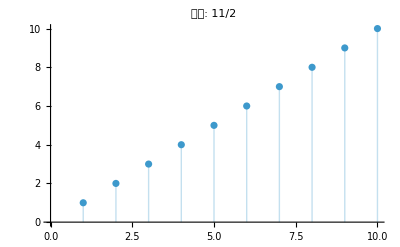

完了。コードを実行して確認し、必要なら ContinueEval で継続できます。

```mathematica
meanVal = Mean[Range[10]]

ListPlot[Range[10], PlotLabel -> Row[{"平均: ", meanVal}], Filling -> Axis]
```

```mathematica
nodes=NotebookLLMGraphNodes[]
lastID=Last[SortBy[Keys[nodes],nodes[#]["Step"]&]]
nodes[lastID][[{"L2Ref","L2NodeCount","L2ErrorCount"}]]
```

<|history-1→<|NodeID→history-1,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{},OutEdges→{<|To→history-2,Type→ContextInheritance|>},Step→0,Time→3.9834241532069629×10^9,Type→query,Instruction→ClaudeQuery/ClaudeEval/ClaudeUpdatePackage/ClaudeUpdateDocumentationなどのLLMを呼び出す関数は、今後の更新で非常に複雑な呼び出し関係を扱う必要が出てくるだろう。そのときのためにLLMGraphオブジェクトに準拠したオブジェクトを生成して、ClaudCodeやLMStudioなどのアクセスレベル付きの呼び出しを扱うようにできないだろうか？
https://reference.wolfram.com/language/ref/LLMGraph.html
をしらべて検証してほしい。
,ResponseSummary→# LLMGraph の調査と ClaudeCode パッケージへの適用可能性

## LLMGraph の概要

`LLMGraph` は Wolfram Language 14.3（2025年8月）で導入された、LLM 呼び出しをDAG（有向非巡回グラフ）として定義・実行するフレームワークです。

### 基本構造

- ノードは `Association` で定義し、以下のいずれか1つを持つ:
  - `"LLMFunction"` — LLM プロンプトを実行するノード
  - `"ListableLLMFunction"` — リスト入力をスレッド化して並列実行するノード
  - `,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-2→<|NodeID→history-2,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-1,Type→ContextInheritance|>},OutEdges→{<|To→history-3,Type→ContextInheritance|>},Step→1,Time→3.9834282554991909×10^9,Type→query,Instruction→InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノートブックLLMGraphをノートブックに保持し、それらのノードやエッジの情報に、既存の履歴情報を対応させることを考えたい。詳細に分析して仕様を策定してほしい。,ResponseSummary→指示: InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノー
応答: # ノートブック LLMGraph 仕様

## 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeE,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-3→<|NodeID→history-3,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-2,Type→ContextInheritance|>},OutEdges→{<|To→history-4,Type→ContextInheritance|>},Step→2,Time→3.9834286036469621×10^9,Type→query,Instruction→各ノードが発火したタイムスタンプ履歴を持つ必要があると思う。,ResponseSummary→指示: InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノー
応答: # ノートブック LLMGraph 仕様

## 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeE,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-4→<|NodeID→history-4,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-3,Type→ContextInheritance|>},OutEdges→{<|To→history-5,Type→ContextInheritance|>},Step→3,Time→3.9834288028874452×10^9,Type→query,Instruction→各ノードが発火したタイムスタンプ履歴を持つ必要があると思う。
各ClaudeQuery/ClaudeEvalなどの実行が完了するとそのジョブは完了することになるが、ContinueEvalなどが存在すると、ClaudeEval/ContinueEvalのセッションがクラスターとして部分グラフを形成している。どこかの結果を使用してプロンプトを生成したり、ユーザが選択Evalなどを指定した場合は、暗黙または明示的な辺が形成されることになるはずである。,ResponseSummary→指示: InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノー
応答: # ノートブック LLMGraph 仕様

## 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeE,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-5→<|NodeID→history-5,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-4,Type→ContextInheritance|>},OutEdges→{<|To→history-6,Type→ContextInheritance|>},Step→4,Time→3.9834290617998334×10^9,Type→query,Instruction→このノートブックネットグラフを表形式やグラフ形式で可視化するツール群を提供し、新モデルでの再計算や計算が停止している部分からの復帰などの処理を容易にするツールを提供する。,ResponseSummary→指示: InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノー
応答: # ノートブック LLMGraph 仕様

## 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeE,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-6→<|NodeID→history-6,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-5,Type→ContextInheritance|>},OutEdges→{<|To→history-7,Type→ContextInheritance|>},Step→5,Time→3.9834297169782537×10^9,Type→query,Instruction→タイムスタンプ履歴だけではなく、稼働した実行スレッドのチェインをタイムスタンプ付きで記録しておく必要があるのではないか。,ResponseSummary→指示: InputNotebookでの作業中に対して、そのノートブックのLLMアクセス全体の、LLMGraphを考えることができる。つまり、単一のClaudeUpdatePackage/ClaudeQuery/ClaudeEvalが、生成するLLMGraphは、実はノートブック全体のLLMGraphの部分グラフである。この考え方でユーザがClaudeQueryを新規に入力し実行する操作もノードと考えたノー
応答: # ノートブック LLMGraph 仕様

## 概念の整理

ノートブックでの作業全体を1つの LLMGraph として捉える。個々の `ClaudeQuery`、`ClaudeE,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-7→<|NodeID→history-7,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-6,Type→ContextInheritance|>},OutEdges→{<|To→history-8,Type→ContextInheritance|>},Step→6,Time→3.9834300486964819×10^9,Type→query,Instruction→履歴サイズの増大を防ぐことが最大の課題である。

その前提のもとに、このLLMGraphとExecutionThreadを主体とした、履歴オブジェクトがLLMの再開やモデル更新後の再実行といった処理を円滑にするスタイルにリファクタリングする必要がある。,ResponseSummary→# 履歴サイズ抑制を軸とした LLMGraph / ExecutionThread リファクタリング設計

## 現行の履歴方式の問題点

現在のセッション履歴はステップごとに `<|"step" -> n, "instruction" -> ..., "response" -> ..., "time" -> ...|>` を蓄積するリスト形式であり、以下の問題がある。

- **線形蓄積**: `ContinueEval` のたびにフルレスポンスが履歴に追加され、`Compress` 後でも数百KB〜数MB に達する
- **重複情報**: `compactN`/`compactW` による,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-8→<|NodeID→history-8,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-7,Type→ContextInheritance|>},OutEdges→{<|To→history-9,Type→ContextInheritance|>},Step→7,Time→3.9834493401696324×10^9,Type→query,Instruction→LLMGraphのExecutionThreadとして
1. ClaudeEvalの呼び出しによるプロンプトベースの計算過程の合成
2. ClaudeEvalが生成するMathematica関数の入出力の結合による計算過程の合成
の二つが、1から2がインスタンス生成されるように合成される。

1はIn[_]をノードに持つグラフであり、2は1が生成した値(Out[_])とMathematica関数(In[_])をノードに持つグラフとなり、In[_]ノード一つに対して、一つ以上複数のOut[_]やIn[_]が対応している。この対応はLLMの入出力で対応している。実際に自動計算過程はIn[_]のみのExecutionThreadか、それが生成した、Out[_]とIn[_]からなるExecutionThreadのどちらかで、最終的な計算過程はOut[_]が結合したものである。

しかしこの分析から、LLMプロンプトによるIn[_]の構成するグラフが、そのノートブック上で行われる計算の概要を示しており、それが生成するOut[_]とIn[_]が実際に実行される計算過程を示す。

再計算やエラー訂正,ResponseSummary→まず添付ファイルの詳細を確認します。# LLMGraph Compositional System: 二層計算過程合成の仕様と実装計画

## 1. 概念の整理: 二層 ExecutionThread

### 1.1 レイヤー L1: プロンプトグラフ（計算の概要）

ノートブック上で発行される `ClaudeEval`/`ClaudeQuery` の呼び出し列が構成するグラフ。ノードは $\text{In}[n]$（LLMへのプロンプト入力セル）であり、ユーザの意図・指示を表す。このグラフは**計算過程の設計図**に相当する。

- 各 $\text{In}[n]$ ノードは1つの Cla,Status→Completed,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>,history-9→<|NodeID→history-9,NodeType→Orchestrator,AccessLevel→ClaudeCode,InEdges→{<|From→history-8,Type→ContextInheritance|>},OutEdges→{},Step→8,Time→3.9834511873233674×10^9,Type→query,Instruction→Range[10] の平均と ListPlot を作成して,ResponseSummary→,Status→Processing,BackupRef→None,L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>|>

history-9

<|L2Ref→None,L2NodeCount→0,L2ErrorCount→0|>

```mathematica
NotebookLLMGraphPlotL2[lastID]
```

L2 キャッシュなし: history-9

```mathematica
NotebookLLMGraphFetchL2[lastID]
```

Missing[CacheExpired]

```mathematica
NotebookLLMGraphErrors[]
```

✅ L2 エラーなし

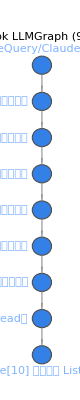

```mathematica
NotebookLLMGraphPlot[]
```